```mathematica
<<Local`QFTToolKit`
Put[SaveFile=NBname["stub"]<>".out"]
```

```mathematica
DefineTensor[α,T,y,x,V,u,U,c,p0,p1,p2]
kgd[i_]:=T[Subscript[k, g],"d"][i]
kgu[i_]:=T[Subscript[k, g],"u"][i]
```

Final Project 1. Peskin-Schroeder p.260

General graphic definitions for array points and lines.

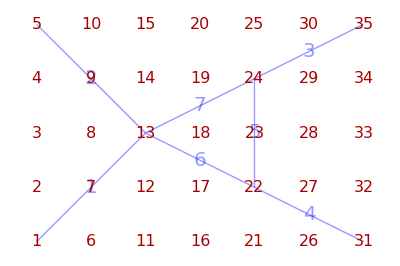

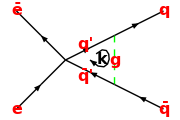
A simple gluon(B)-quark(ψ) coupling model is Δℋ→IntegralOp[{{x_1^1},g OverBar[ψ_{f,i}].γ_μ^μ.ψ_{f,i}.B_μ^μ}] where flavor:f→{u,d,s,c,b,t} and color:i→{1,2,3} and strong coupling constant g is independant of {f,i} and the EM coupling is {Q_(u|c|t)→2/3,Q_(d|s|b)→-1/3}. Also define: α_g→g^2/(4 π)
Compute the diagram contributing to {e^-,e^+}→{q̄,q} involving one virtual gluon. {e^-,e^+}→{q̄',q',g}→{q̄,q} where {q̄',q',g} is the loop -Graphics-

```mathematica
PR1["A simple gluon(B)-quark(ψ) coupling model is ",
Δℋ->IntegralOp[{{x@u[timespace[1]]},g OverBar[Subscript[ψ, {f,i}]].γ@u[μ].Subscript[ψ, {f,i}].B@d[μ]}],
" where flavor:",f->{u,d,s,c,b,t}," and color:",i->{1,2,3}," and strong coupling constant g is independant of {f,i} and the EM coupling is ",
subQ={Subscript[Q, u|c|t]->2/3,Subscript[Q, d|s|b]->-1/3},
". Also define: ",Subscript[α, g]->g^2/(4π),
NL,"Compute the diagram contributing to ",{SuperMinus[e],SuperPlus[e]}->{q̄,q}," involving one virtual gluon. ",
{SuperMinus[e],SuperPlus[e]}->{q̄',q',g}->{q̄,q},
" where ",{q̄',q',g}," is the loop ",
{vx,line}=GraphicPointLines[7,5,{{1,13},{5,13},{24,35},{22,31},{24,22},{13,22},{13,24}}];
Linex[i_]:=Line[line[[i]]];
font:={Red,Bold,16};
Graphics[{Thin,Black,
MidArrow[line[[1]]],
MidArrow[line[[2]]//Reverse],
MidArrow[line[[3]]],
MidArrow[line[[4]]//Reverse],
{Dashed,Green,Thick,Linex[5]},
MidArrow[line[[7]]],
MidArrow[line[[6]]//Reverse],
Text[Style[e,font],vx[[1]]],
Text[Style[ē,font],vx[[5]]],
Text[Style[q,font],vx[[35]]],
Text[Style[q̄,font],vx[[31]]],
Text[Style[g,font],vx[[23]]],
MidLineTextOffset[q',vx[[18]],font,{0.3,.15}],
MidLineTextOffset[q̄',vx[[18]],font,{0.3,-1.15}],
Arrow[BezierCurve[{(1.5vx[[18]]+.5vx[[24]])/2,vx[[24]],vx[[22]],vx[[18]]}]],
Text[Style[k,{Bold,16}],vx[[18]]+{.5,0}]
},ImageSize->Small]
]
```

```mathematica
PR1["The contribution to the scattering amplitude from the above loop diagram (similar to PS.6.38): ",
tmpM=δℳ->IntegralOp[{{T[Subscript[k, g],"u"][μ]}},1/(2π)^4
 Dot[OverBar[Subscript[v, e]][Subscript[p, SuperPlus[e]]],-I e γ@u[μe],Subscript[u, e][Subscript[p, SuperMinus[e]]] ].
(-I g@uu[μg,νg]/(Subscript[k, g]^2-Subscript[m, g]^2+I ϵ)).
Dot[OverBar[Subscript[u, q]][Subscript[p, q]],-I g γ@d[μg] ].
(I(Slash[Subscript[p, q']]+Subscript[m, q'])/(Subscript[p, q']^2-Subscript[m, q']^2+I ϵ)).
(-I e γ@d[μe] ).
(I(Slash[Subscript[p, OverBar[q']]]+Subscript[m, OverBar[q']])/(Subscript[p, OverBar[q']]^2-Subscript[m, OverBar[q']]^2+I ϵ)).
Dot[-I g γ@d[νg],Subscript[v, q][Subscript[p, q̄]] ]
],
NL,"where we have retained the EM vector boson connection between {e,e} and {q',q'}."
]
```

The contribution to the scattering amplitude from the above loop diagram (similar to PS.6.38): δℳ→∫_{k_g_μ^μ} [1/(16 π^4)OverBar[v_e][p_(e^+)].(-ⅈ e γ_μe^μe).u_e[p_(e^-)].(-(ⅈ g_μgνg^μgνg)/(ⅈ ϵ+k_g^2-m_g^2)).OverBar[u_q][p_q].(-ⅈ g γ_μg^μg).(ⅈ (/p_q'+m_q'))/(ⅈ ϵ-m_q'^2+p_q'^2).(-ⅈ e γ_μe^μe).(ⅈ (/p_OverBar[q']+m_OverBar[q']))/(ⅈ ϵ-m_OverBar[q']^2+p_OverBar[q']^2).(-ⅈ g γ_νg^νg).v_q[p_(q̄)]]
where we have retained the EM vector boson connection between {e,e} and {q',q'}.

```mathematica
PR1["Scalars",scalar={e,g,g@uu[_,_]},
Imply,tmp=tmpM//.simpleDot2[{scalar}],
Imply,tmp=tmp/.IntegralOp[a_,b_]:>IntegralOp[a,MetricContract[g][b]],
NL,"Substitute in integration variable:",
subk={Subscript[k, g]^2->g@dd[μk,νk]T[Subscript[k, g],"u"][μk]T[Subscript[k, g],"u"][νk],Slash[Subscript[p, q']]->Slash[Subscript[p, q]]-Slash[Subscript[k, g]],Slash[Subscript[p, OverBar[q']]]->Slash[Subscript[p, q̄]]+Slash[Subscript[k, g]],Subscript[p, q']^2->(Subscript[p, q]-Subscript[k, g]).(Subscript[p, q]-Subscript[k, g]),Subscript[p, OverBar[q']]^2->(Subscript[p, q̄]+Subscript[k, g]).(Subscript[p, q̄]+Subscript[k, g])},
Imply,tmp=tmp/.subk,
Imply,tmpM1=tmp /.dot:HoldPattern[Dot[a_,b__]]:>SeparateInto2After[Subscript[u, e][_]][dot]  //IntegrandWithout[{Subscript[k, g]}]
];
```

Scalars{e,g,g___^__}
⇒ δℳ→∫_{k_g_μ^μ} [(ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)].1/(ⅈ ϵ+k_g^2-m_g^2).OverBar[u_q][p_q].γ_μg^μg.(/p_q'+m_q')/(ⅈ ϵ-m_q'^2+p_q'^2).γ_μe^μe.(/p_OverBar[q']+m_OverBar[q'])/(ⅈ ϵ-m_OverBar[q']^2+p_OverBar[q']^2).γ_νg^νg.v_q[p_(q̄)] g_μgνg^μgνg)/(16 π^4)]
⇒ δℳ→∫_{k_g_μ^μ} [(ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)].1/(ⅈ ϵ+k_g^2-m_g^2).OverBar[u_q][p_q].γ_νg^νg.(/p_q'+m_q')/(ⅈ ϵ-m_q'^2+p_q'^2).γ_μe^μe.(/p_OverBar[q']+m_OverBar[q'])/(ⅈ ϵ-m_OverBar[q']^2+p_OverBar[q']^2).γ_νg^νg.v_q[p_(q̄)])/(16 π^4)]
Substitute in integration variable:{k_g^2→g_μkνk^μkνk k_g_μk^μk k_g_νk^νk,/p_q'→-(/k_g)+/p_q,/p_OverBar[q']→/k_g+/p_(q̄),p_q'^2→(-k_g+p_q).(-k_g+p_q),p_OverBar[q']^2→(k_g+p_(q̄)).(k_g+p_(q̄))}
⇒ δℳ→∫_{k_g_μ^μ} [1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)].1/(ⅈ ϵ-m_g^2+g_μkνk^μkνk k_g_μk^μk k_g_νk^νk).OverBar[u_q][p_q].γ_νg^νg.(-(/k_g)+/p_q+m_q')/(ⅈ ϵ+(-k_g+p_q).(-k_g+p_q)-m_q'^2).γ_μe^μe.(/k_g+/p_(q̄)+m_OverBar[q'])/(ⅈ ϵ+(k_g+p_(q̄)).(k_g+p_(q̄))-m_OverBar[q']^2).γ_νg^νg.v_q[p_(q̄)]]
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_{k_g_μ^μ} [1/(ⅈ ϵ-m_g^2+g_μkνk^μkνk k_g_μk^μk k_g_νk^νk).OverBar[u_q][p_q].γ_νg^νg.(-(/k_g)+/p_q+m_q')/(ⅈ ϵ+(-k_g+p_q).(-k_g+p_q)-m_q'^2).γ_μe^μe.(/k_g+/p_(q̄)+m_OverBar[q'])/(ⅈ ϵ+(k_g+p_(q̄)).(k_g+p_(q̄))-m_OverBar[q']^2).γ_νg^νg.v_q[p_(q̄)]]

```mathematica
PR1["Feynmann Parameterization:",
tmp=tmpM1;
Imply,pos=ExtractPositionPattern[tmp,HoldPattern[Dot[__]]];
Imply,tmpFeyn=pos[[4,2]]=FeynmannParameterization[pos[[4,2]]]//Last;
Imply,tmpM2=ReplacePart[tmp,pos[[4]]]
];
```

Feynmann Parameterization:
⇒ 
⇒ 
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_{k_g_μ^μ} [1.OverBar[u_q][p_q].γ_νg^νg.(-(/k_g)+/p_q+m_q').γ_μe^μe.(/k_g+/p_(q̄)+m_OverBar[q']).γ_νg^νg.v_q[p_(q̄)] ∫_({x_1,0,1}
{x_2,0,1}
{x_3,0,1}) [(2 δ[-1+x_1+x_2+x_3])/((ⅈ ϵ+(k_g+p_(q̄)).(k_g+p_(q̄))-m_OverBar[q']^2) x_1+(ⅈ ϵ+(-k_g+p_q).(-k_g+p_q)-m_q'^2) x_2+x_3 (ⅈ ϵ-m_g^2+g_μkνk^μkνk k_g_μk^μk k_g_νk^νk))^3]]

```mathematica
PR1["Examine Feynmann Parameterization Expression, CompleteSquare: ",
"POFF",
posFey=ExtractPositionPattern[tmpFeyn,IntegralOp[_,_]],
Yield,tmp=posFey[[1,2]],
NL,"Substitute: ",sub={Subscript[p, a_]. Subscript[p, a_]->Subscript[m, a]^2,Subscript[m, q'|OverBar[q']|q̄]->Subscript[m, q]},
Yield,tmp=tmp//.simpleDot2[{}]/.dot:Dot[a_,b_]:>orderArg[dot]//.sub,
NL,"The Dot products represent 4-vector products: ",sub={Dot[a_,b_]:>g@dd[μ[a,b],ν[a,b]]T[a,"u"][μ[a,b]]T[b,"u"][ν[a,b]]},
Yield,tmp=tmp/.sub,
NL,"Extract and Simplify Denominator: ",sub={Subscript[x, 3]->1-Subscript[x, 1]-Subscript[x, 2]},
Yield,test=tmpd=tmp[[2]]//Denominator,
Yield,tmpd1=tmpd[[1]]/.sub//Expand//ContractUpDn[g],
Yield,tmpd1=tmpd1/.{term:(T[Subscript[k, g],"d"][a_]rest__):>(term/.a->ik)},
NL,"Complete the square of this: ",
Yield,tmpd1Sq=CompleteSquareUpDn[tmpd1,T[Subscript[k, g],"d"][ik]],check,
Yield,tmpd[[1]]=tmpd1Sq[[1]],check,
Yield,posFey[[1,2,2]]=tmp[[2,2]]=Numerator[tmp[[2]]]/tmpd,
Yield,tmp=ReplacePart[tmpFeyn,posFey],
Yield,pos[[4,2]]=ReplacePart[tmpFeyn,posFey]/.δ[_]->1/.{IntegralOp[a_,b_]:>IntegralOp[DeleteCases[a,{Subscript[x, 3],_,_}],b]}/.{Subscript[x, 2],0,1}->{Subscript[x, 2],0,1-Subscript[x, 1]},

Imply,tmpM3=ReplacePart[tmpM2,pos[[4]]]/.IntegralOp[a_,b_](gt:g@uu[c_,d_])->IntegralOp[a,gt b ],
"PONdd",
Imply,tmpM3=tmpM3/.IntegralOp[a_,b_ IntegralOp[c_,d_]]->IntegralOp[c,IntegralOp[a,b d]]
];
```

Examine Feynmann Parameterization Expression, CompleteSquare: 
.......
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [∫_{k_g_μ^μ} [(2 1.OverBar[u_q][p_q].γ_νg^νg.(-(/k_g)+/p_q+m_q').γ_μe^μe.(/k_g+/p_(q̄)+m_OverBar[q']).γ_νg^νg.v_q[p_(q̄)])/((k_g_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)) (k_g_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik))+1/4 (4 (ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2)-(-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik) (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)))^3]]

```mathematica
PR1["Change integration variable to l's: ",
Yield,tmpoff={tmpd1Sq[[3]]},
yield,subls=Thread[{kgd[ik_],kgu[ik_]}->{l@d[ik],l@u[ik]}-Join[tmpoff,(tmpoff/.sRaiseAllIndices[{}])]]/.ik->μk//Simplify,
Imply,tmp=tmpM31=tmpM3/.subls,
NL,"Expand the k dependent Numerator in l's: ",
"xPOFF",
Yield,numpos=ExtractPositionPattern[tmp,HoldPattern[Dot[__]]  ],
Yield,tmpnum=numpos[[2,2]]/.Slash[a_]:>T[a,"d"][$i=Unique[μ]]T[γ,"u"][$i]/.subls//DotExpandAll;
Yield,tmpnum=tmpnum//.simpleDot2[{Subscript[x, _],Subscript[m, _],T[(Subscript[p, _]|l),"d"][_]}]//TensorSimplify,
Yield,tmp2=tmpnum//.HoldPattern[u_[uc_]. a__ . v_[vc_]]:>Dot[a]//Simplify//Expand,
NL,"Use symmetry of integrand to eliminate odd powers of l.",
Yield,tmp2=Map[Switch[
 Count[#, T[l,"d"][_] ],
0,#,
1,0,
2,#/.T[l,"d"][i_]T[l,"d"][j_]:>g@dd[i,j]T[l,"d"][μl]T[l,"u"][μl]/4]&,tmp2]//Simplify,
Yield,tmp1=tmpnum/.HoldPattern[u_[uc_]. a__ . v_[vc_]]:>Dot[u[uc],v[vc]]//Simplify;
Yield,save=numpos[[2,2]]=tmp1/.Dot[u_,v_]rest__:>Dot[u,tmp2,v],
"PONdd",
Yield,tmpM4=ReplacePart[tmpM31,numpos]
];
SimplifyAmplitude[exp_]:=Module[{tmp=exp,tmp1,
scalars={Subscript[m, _],T[Subscript[p, _],"d"][_],g@uu[_,_],η@uu[_,_],η@ud[_,_],Subscript[x, _],l@u[_],l@d[_]},
sub1=(op:dotOps)[up_[pu_],d__  , vp_[pv_]]( p:(T[pu_,"d"][pi_]) )a___:>
op[up[pu] ,GammaLeft[γ@u[pi]][Dot[d]] ,vp[pv]]p a,
sub1r=(op:dotOps)[up_[pu_],d__  ,vp_[pv_]]( p:(T[pv_,"d"][pi_]) )a___:>
op[up[pu] ,GammaRight[γ@u[pi]][Dot[d]] ,vp[pv]]p a,
subm={
(dot:dotOps)[up_[pu_],γ@u[pi_],a___]T[pu_,"d"][pi_]rest___:>dot[up[pu],a] Subscript[m, pu[[2]]] rest,(dot:dotOps)[a__,γ@u[pi_],vp_[pv_]]T[pv_,"d"][pi_]rest___:>dot[a,vp[pv]] Subscript[m, pv[[2]]] rest
},
subsw=(term:((dotOps)[a__]T[pv_,"u"][pi_]rest___)):>UpDownIndexSwap[pi][term]
},
Do[
tmp=tmp//simpleDot3[scalars];
tmp=tmp/.sub1//simpleDot3[scalars]//MetricContractAll[η];
tmp=tmp/.sub1r//simpleDot3[scalars]//MetricContractAll[η];
tmp=tmp/.subsw//.subm//TensorSimplify;
tmp=tmp//.psA29//simpleDot3[scalars]//TensorSimplify,
{3}];
tmp
];
PR1["Further Simplify Numerator with: ",(subm={HoldPattern[T[p1_,"d"][i1_]T[p2_,"u"][i1_]]:>T[p1,"d"][orderArg[μ[p1,p2]]]T[p2,"u"][orderArg[μ[p1,p2]]],(pp:T[p1_,"u"][i1_]T[p2_,"d"][i1_]):>Swap[{p1,p2}][pp]/;!OrderedQ[{p1,p2}],(pp:T[Subscript[p, i_],"d"][i1_]T[Subscript[p, i_],"u"][i1_])->Subscript[m, i]^2,Subscript[m, q|q'|q̄|OverBar[q']]->Subscript[m, q]}
)//Column,  (*TensorSimplify does not do the job.*)
tmp=numpos[[2,2]];
tmp=tmp//DotExpandAll//MetricContractAll[g];
numpos[[2,2]]=tmp=Map[SimplifyAmplitude[#]&,tmp]//TensorSimplify//Simplify;
numpos=numpos//.subm;
Imply,tmpM4=ReplacePart[tmpM31,numpos]
];
Save[SaveFile,{SimplifyAmplitude,save}]
```

Change integration variable to l's: 
→ {1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)} ⟶ {k_g_μk_^μk_→l_μk^μk+x_2 p_q_μk^μk-x_1 (p_(q̄))_μk^μk,k_g_μk_^μk_→l_μk^μk+x_2 p_q_μk^μk-x_1 (p_(q̄))_μk^μk}
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [∫_{l_μ^μ+x_2 p_q_μ^μ-x_1 (p_(q̄))_μ^μ} [(2 1.OverBar[u_q][p_q].γ_νg^νg.(-(/k_g)+/p_q+m_q').γ_μe^μe.(/k_g+/p_(q̄)+m_OverBar[q']).γ_νg^νg.v_q[p_(q̄)])/((l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)) (l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik))+1/4 (4 (ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2)-(-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik) (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)))^3]]
Expand the k dependent Numerator in l's: xPOFF
→ {{2,5}→OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)],{2,6,2,2,2}→1.OverBar[u_q][p_q].γ_νg^νg.(-(/k_g)+/p_q+m_q').γ_μe^μe.(/k_g+/p_(q̄)+m_OverBar[q']).γ_νg^νg.v_q[p_(q̄)]}
→ 
→ OverBar[u_q][p_q].γ_νg^νg.γ_μe^μe.γ_νg^νg.v_q[p_(q̄)] m_OverBar[q'] m_q'-OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg.v_q[p_(q̄)] m_OverBar[q'] l_μ$12169^μ$12169+OverBar[u_q][p_q].γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] m_q' l_μ$12175^μ$12175-OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] l_μ$12169^μ$12169 l_μ$12175^μ$12175-OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg.v_q[p_(q̄)] m_OverBar[q'] (-1+x_2) p_q_μ$12169^μ$12169-OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] (-1+x_2) l_μ$12175^μ$12175 p_q_μ$12169^μ$12169+OverBar[u_q][p_q].γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] m_q' x_2 p_q_μ$12175^μ$12175-OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] x_2 l_μ$12169^μ$12169 p_q_μ$12175^μ$12175-OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] (-1+x_2) x_2 p_q_μ$12169^μ$12169 p_q_μ$12175^μ$12175+OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg.v_q[p_(q̄)] m_OverBar[q'] x_1 (p_(q̄))_μ$12169^μ$12169+OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] x_1 l_μ$12175^μ$12175 (p_(q̄))_μ$12169^μ$12169+OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] x_1 x_2 p_q_μ$12175^μ$12175 (p_(q̄))_μ$12169^μ$12169-OverBar[u_q][p_q].γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] m_q' (-1+x_1) (p_(q̄))_μ$12175^μ$12175+OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] (-1+x_1) l_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175+OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] (-1+x_1) (-1+x_2) p_q_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175-OverBar[u_q][p_q].γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg.v_q[p_(q̄)] (-1+x_1) x_1 (p_(q̄))_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175
→ γ_νg^νg.γ_μe^μe.γ_νg^νg m_OverBar[q'] m_q'-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] l_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' l_μ$12175^μ$12175-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg l_μ$12169^μ$12169 l_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] p_q_μ$12169^μ$12169-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_2 p_q_μ$12169^μ$12169+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg l_μ$12175^μ$12175 p_q_μ$12169^μ$12169-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_2 l_μ$12175^μ$12175 p_q_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_2 p_q_μ$12175^μ$12175-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_2 l_μ$12169^μ$12169 p_q_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_2 p_q_μ$12169^μ$12169 p_q_μ$12175^μ$12175-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_2^2 p_q_μ$12169^μ$12169 p_q_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_1 (p_(q̄))_μ$12169^μ$12169+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_1 l_μ$12175^μ$12175 (p_(q̄))_μ$12169^μ$12169+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_1 x_2 p_q_μ$12175^μ$12175 (p_(q̄))_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_1 (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg l_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_1 l_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg p_q_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_1 p_q_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_2 p_q_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_1 x_2 p_q_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_1 (p_(q̄))_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg x_1^2 (p_(q̄))_μ$12169^μ$12169 (p_(q̄))_μ$12175^μ$12175
Use symmetry of integrand to eliminate odd powers of l.
→ γ_νg^νg.γ_μe^μe.γ_νg^νg m_OverBar[q'] m_q'+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] p_q_μ$12169^μ$12169-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_2 p_q_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_2 p_q_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_1 (p_(q̄))_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_1 (p_(q̄))_μ$12175^μ$12175-1/4 γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg (g_μ$12169μ$12175^μ$12169μ$12175 l_μl^μl l_μl^μl+4 ((-1+x_2) p_q_μ$12169^μ$12169-x_1 (p_(q̄))_μ$12169^μ$12169) (x_2 p_q_μ$12175^μ$12175-(-1+x_1) (p_(q̄))_μ$12175^μ$12175))
→ 
→ OverBar[u_q][p_q].(γ_νg^νg.γ_μe^μe.γ_νg^νg m_OverBar[q'] m_q'+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] p_q_μ$12169^μ$12169-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_2 p_q_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_2 p_q_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_1 (p_(q̄))_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_1 (p_(q̄))_μ$12175^μ$12175-1/4 γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg (g_μ$12169μ$12175^μ$12169μ$12175 l_μl^μl l_μl^μl+4 ((-1+x_2) p_q_μ$12169^μ$12169-x_1 (p_(q̄))_μ$12169^μ$12169) (x_2 p_q_μ$12175^μ$12175-(-1+x_1) (p_(q̄))_μ$12175^μ$12175))).v_q[p_(q̄)]PONdd
→ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [∫_{l_μ^μ+x_2 p_q_μ^μ-x_1 (p_(q̄))_μ^μ} [(2 OverBar[u_q][p_q].(γ_νg^νg.γ_μe^μe.γ_νg^νg m_OverBar[q'] m_q'+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] p_q_μ$12169^μ$12169-γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_2 p_q_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_2 p_q_μ$12175^μ$12175+γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_νg^νg m_OverBar[q'] x_1 (p_(q̄))_μ$12169^μ$12169+γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' (p_(q̄))_μ$12175^μ$12175-γ_νg^νg.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg m_q' x_1 (p_(q̄))_μ$12175^μ$12175-1/4 γ_νg^νg.γ_μ$12169^μ$12169.γ_μe^μe.γ_μ$12175^μ$12175.γ_νg^νg (g_μ$12169μ$12175^μ$12169μ$12175 l_μl^μl l_μl^μl+4 ((-1+x_2) p_q_μ$12169^μ$12169-x_1 (p_(q̄))_μ$12169^μ$12169) (x_2 p_q_μ$12175^μ$12175-(-1+x_1) (p_(q̄))_μ$12175^μ$12175))).v_q[p_(q̄)])/((l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)) (l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik))+1/4 (4 (ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2)-(-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik) (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)))^3]]

Further Simplify Numerator with: HoldPattern[T[p1_,d][i1_] T[p2_,u][i1_]]:>T[p1,d][orderArg[μ[p1,p2]]] T[p2,u][orderArg[μ[p1,p2]]]
pp:p1__i1_^i1_ p2__i1_^i1_:>Swap[{p1,p2}][pp]/;!OrderedQ[{p1,p2}]
pp:p_i__i1_^i1_ p_i__i1_^i1_→m_i^2
m_(q|q'|q̄|OverBar[q'])→m_q
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [∫_{l_μ^μ+x_2 p_q_μ^μ-x_1 (p_(q̄))_μ^μ} [(2 (-4 OverBar[u_q][p_q].v_q[p_(q̄)] (-(m_q+m_q (-1+x_2)) (x_2 p_q_μe^μe-(-1+x_1) (p_(q̄))_μe^μe)+m_q ((-1+x_2) p_q_μe^μe-x_1 (p_(q̄))_μe^μe)-m_q (-1+x_1) (-(-1+x_2) p_q_μe^μe+x_1 (p_(q̄))_μe^μe))-OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (2 m_q^2-2 m_q^2 x_1+2 m_q^2 x_1^2+2 m_q^2 (-1+x_2) x_2+2 m_q^2 (-1+x_1+x_2)+l_μl^μl l_μl^μl-4 p_q_νg^νg (p_(q̄))_νg^νg+4 x_1 p_q_νg^νg (p_(q̄))_νg^νg+4 x_2 p_q_νg^νg (p_(q̄))_νg^νg-4 x_1 x_2 p_q_νg^νg (p_(q̄))_νg^νg)))/((l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)) (l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik))+1/4 (4 (ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2)-(-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik) (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)))^3]]

```mathematica
PR1["Test PS claim that the Denominator is even in {x_1,x_2}. Swap {x_1,x_2} and take ratio: ",
tmp=ExtractPattern[tmpM4,IntegralOp[{{__},{__}},__]][[1,2]]//Denominator,
"POFF",
Yield,tmp1=tmp//Swap[{Subscript[x, 1],Subscript[x, 2]}],
Yield,tmp=tmp/tmp1,
Yield,tmp=tmp^(1/3)//PowerExpand//Simplify,
"PON",
imply,{(tmp//.subm)->1,OK,"even"}
]
```

Test PS claim that the Denominator is even in {x_1,x_2}. Swap {x_1,x_2} and take ratio: 1 ⇒ {1→1, OK ,even}

```mathematica
PR1["Test PS claim of odd Numerator component in q: ",
Yield,tmp=numpos[[2,2]],
Yield,tmp1=tmp//Swap[{Subscript[x, 1],Subscript[x, 2]}],
Yield,tmp-tmp1//Simplify,CR["<-Odd component is zero upon {x_1,x_2} integration."],
NL,"The Even component: ",
numpos[[2,2]]=(tmp+tmp1)/2//Simplify,
Imply,tmpM5=ReplacePart[tmpM31,numpos],
NL,"Simplify Denominator: ",
Yield,pos=ExtractPositionPattern[tmpM5,(_)^(-3)],
Yield,tmp=pos[[1,2]]^(1/3)//PowerExpand,
Yield,tmpi=1/tmp//Expand,
Yield,pos[[1,2]]=(1/tmpi)^3,
Imply,tmpM5=ReplacePart[tmpM5,pos]//.subm
];
```

Test PS claim of odd Numerator component in q: 
→ -4 OverBar[u_q][p_q].v_q[p_(q̄)] (-(m_q+m_q (-1+x_2)) (x_2 p_q_μe^μe-(-1+x_1) (p_(q̄))_μe^μe)+m_q ((-1+x_2) p_q_μe^μe-x_1 (p_(q̄))_μe^μe)-m_q (-1+x_1) (-(-1+x_2) p_q_μe^μe+x_1 (p_(q̄))_μe^μe))-OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (2 m_q^2-2 m_q^2 x_1+2 m_q^2 x_1^2+2 m_q^2 (-1+x_2) x_2+2 m_q^2 (-1+x_1+x_2)+l_μl^μl l_μl^μl-4 p_q_νg^νg (p_(q̄))_νg^νg+4 x_1 p_q_νg^νg (p_(q̄))_νg^νg+4 x_2 p_q_νg^νg (p_(q̄))_νg^νg-4 x_1 x_2 p_q_νg^νg (p_(q̄))_νg^νg)
→ -4 OverBar[u_q][p_q].v_q[p_(q̄)] (-(m_q+m_q (-1+x_1)) (x_1 p_q_μe^μe-(-1+x_2) (p_(q̄))_μe^μe)+m_q ((-1+x_1) p_q_μe^μe-x_2 (p_(q̄))_μe^μe)-m_q (-1+x_2) (-(-1+x_1) p_q_μe^μe+x_2 (p_(q̄))_μe^μe))-OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (2 m_q^2+2 m_q^2 (-1+x_1) x_1-2 m_q^2 x_2+2 m_q^2 x_2^2+2 m_q^2 (-1+x_1+x_2)+l_μl^μl l_μl^μl-4 p_q_νg^νg (p_(q̄))_νg^νg+4 x_1 p_q_νg^νg (p_(q̄))_νg^νg+4 x_2 p_q_νg^νg (p_(q̄))_νg^νg-4 x_1 x_2 p_q_νg^νg (p_(q̄))_νg^νg)
→ -4 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (-x_1+x_1^2+x_2-x_2^2) (p_q_μe^μe-(p_(q̄))_μe^μe)<-Odd component is zero upon {x_1,x_2} integration.
The Even component: 2 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)-OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (2 m_q^2 (x_1^2+x_2^2)+l_μl^μl l_μl^μl-4 (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg)
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [∫_{l_μ^μ+x_2 p_q_μ^μ-x_1 (p_(q̄))_μ^μ} [(2 (2 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)-OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (2 m_q^2 (x_1^2+x_2^2)+l_μl^μl l_μl^μl-4 (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg)))/((l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)) (l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik))+1/4 (4 (ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2)-(-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik) (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)))^3]]
Simplify Denominator: 
→ {{2,6,2,2,2}→1/((l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)) (l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik))+1/4 (4 (ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2)-(-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik) (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)))^3}
→ 1/((l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)) (l_ik^ik+x_2 p_q_ik^ik-x_1 (p_(q̄))_ik^ik+1/2 (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik))+1/4 (4 (ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2)-(-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik) (-2 x_2 p_q_ik^ik+2 x_1 (p_(q̄))_ik^ik)))
→ ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2+l_ik^ik l_ik^ik-x_2^2 p_q_ik^ik p_q_ik^ik+x_1 x_2 p_q_ik^ik (p_(q̄))_ik^ik+x_1 x_2 p_q_ik^ik (p_(q̄))_ik^ik-x_1^2 (p_(q̄))_ik^ik (p_(q̄))_ik^ik
→ 1/((ⅈ ϵ-m_g^2+m_g^2 x_1+m_g^2 x_2+l_ik^ik l_ik^ik-x_2^2 p_q_ik^ik p_q_ik^ik+x_1 x_2 p_q_ik^ik (p_(q̄))_ik^ik+x_1 x_2 p_q_ik^ik (p_(q̄))_ik^ik-x_1^2 (p_(q̄))_ik^ik (p_(q̄))_ik^ik)^3)
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [∫_{l_μ^μ+x_2 p_q_μ^μ-x_1 (p_(q̄))_μ^μ} [(2 (2 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)-OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (2 m_q^2 (x_1^2+x_2^2)+l_μl^μl l_μl^μl-4 (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg)))/(ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+l_ik^ik l_ik^ik+2 x_1 x_2 p_q_ik^ik (p_(q̄))_ik^ik)^3]]

```mathematica
PR1["Separate and Simplify the IntegralOp[{{l}},] part: ",
tmp=tmpM5/.IntegralOp[{{a_}},b_]->IntegralOp[{{a[[1]]}},b],
"POFF",
Yield,posLl=ExtractPositionPattern[tmp,IntegralOp[{{l@u[μ]}},b_]],
Yield,tmpintegrand=posLl[[1,2,2]],
NL,"Find Numerator coefficients of ",subll=l@u[μl]l@d[μl]->ll,
Yield,tmpnumer=tmpintegrand/.subll//Numerator//CoefficientList[#,ll]&//Simplify,
Yield,posLl[[1,2,2]]=tmpintegrand=Thread[(tmpnumer/Denominator[tmpintegrand]){1,ll}],
Imply,tmp=posLl/.IntegralOp[{{l@u[μ]}},{b_,c_}]->IntegralOp[{{l@u[μ]}},b]+IntegralOp[{{l@u[μ]}},c]/.Reverse[subll]/.{μl->μ,ik->μ},
"PON",
Imply,posLl=tmp/.IntegralOp[{{l@u[μ]}},a_ b_^-3]:>a IntegralOp[{{l@u[μ]}},1/(b^3)]/;ListFreeQ[a,{{l@u[μ]},{l@d[μ]}}]
/.IntegralOp[{{l@u[μ]}},a_ l@u[μ]l@d[μ]  b_^-3]:>
a IntegralOp[{{l@u[μ]}}, l@u[μ]l@d[μ]  /(b^3)]
]
```

Separate and Simplify the IntegralOp[{{l}},] part: δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [∫_{l_μ^μ} [(2 (2 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)-OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (2 m_q^2 (x_1^2+x_2^2)+l_μl^μl l_μl^μl-4 (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg)))/(ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+l_ik^ik l_ik^ik+2 x_1 x_2 p_q_ik^ik (p_(q̄))_ik^ik)^3]]
⇒ {{2,6,2}→-2 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] ∫_{l_μ^μ} [(l_μ^μ l_μ^μ)/((ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+l_μ^μ l_μ^μ+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)^3)]+∫_{l_μ^μ} [1/((ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+l_μ^μ l_μ^μ+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)^3)] (-4 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] m_q^2 (x_1^2+x_2^2)+4 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)+8 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg)}

```mathematica
PR1["See if Pattern (PS.6.49) matches. ",
(ps649=IntegralOp[{{l@u[μ]}},((Δ_+l@u[μ]l@d[μ])^(m_))]->(2π)^4 (I (-1)^-m)/(4π)^2 (1/((-m-1)(-m-2)))(1/Δ^(-m-2))),
Yield,posLl[[1,2,2]]=posLl[[1,2,2]]/.ps649,
NL,"Do Wick rotation on remaining Integral: ",
posInt=ExtractPositionPattern[posLl,IntegralOp[a_,b_]],
NL,"Apply renormalization PS.6.51: ",ps651=IntegralOp[{{l@u[μ]}},l@u[μ]l@d[μ]((Δ_+l@u[μ]l@d[μ])^(m_))]->IntegralOp[{{l@u[μ]}},l@u[μ]l@d[μ]((Δ+l@u[μ]l@d[μ])^(m))-l@u[μ]l@d[μ]((Δ+Λ^2+l@u[μ]l@d[μ])^(m))],
Yield,tmp=posInt/.ps651,
NL,"Apply Wick rotation: ",subWick={l@u[μ]l@d[μ]->-l@u[μ]l@u[μ],IntegralOp[{{a_}},b1_ (c1_^m_)+b2_(c2_^m_)]:> I/(4π)^2 IntegralOp[{{Ω},{a a}},a^2b1  c1^m+a^2 b2 c2^m],
l@u[μ]->√ll
},
Yield,tmp=tmp//.subWick[[1]]//.subWick[[2;;3]],
NL,"Simplify the integrand by collecting into XXX the term: ",
pos=ExtractPositionPattern[tmp,Plus[-ll,__]];
xterm=pos[[1,2]]+ll,
pos[[1,2]]=pos[[1,2]]-xterm+XXX;
pos[[2,2]]=pos[[2,2]]-xterm+XXX;
tmp=ReplacePart[tmp,pos],
NL,"Integrating: ",
tmp=tmp/.subxIntegrateOne/.{ll}->{ll,0,∞}/.subIntegrate,
NL,"Since XXX !∈ Reals: ",
Yield,posInt=tmp=tmp/.ConditionalExpression[a_,b_]->a/.XXX->xterm
];
```

See if Pattern (PS.6.49) matches. ∫_{l_μ^μ} [(Δ_+l_μ^μ l_μ^μ)^m_]→(ⅈ (-1)^-m π^2 Δ^(2+m))/((-2-m) (-1-m))
→ -(ⅈ π^2 (-4 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] m_q^2 (x_1^2+x_2^2)+4 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)+8 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg))/(2 (ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ))
Do Wick rotation on remaining Integral: {{1,2,1,3}→∫_{l_μ^μ} [(l_μ^μ l_μ^μ)/((ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+l_μ^μ l_μ^μ+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)^3)]}
Apply renormalization PS.6.51: ∫_{l_μ^μ} [l_μ^μ l_μ^μ (Δ_+l_μ^μ l_μ^μ)^m_]→∫_{l_μ^μ} [l_μ^μ l_μ^μ (Δ+l_μ^μ l_μ^μ)^m-l_μ^μ l_μ^μ (Δ+Λ^2+l_μ^μ l_μ^μ)^m]
→ {{1,2,1,3}→∫_{l_μ^μ} [(l_μ^μ l_μ^μ)/((ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+l_μ^μ l_μ^μ+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)^3)-(l_μ^μ l_μ^μ)/((ⅈ ϵ+Λ^2-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+l_μ^μ l_μ^μ+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)^3)]}
Apply Wick rotation: {l_μ^μ l_μ^μ→-(l_μ^μ)^2,∫_{a_} [b1_ c1_^m_+b2_ c2_^m_]:>(ⅈ ∫_({Ω}
{a^2}) [a^2 b1 c1^m+a^2 b2 c2^m])/(4 π)^2,l_μ^μ→√ll}
→ {{1,2,1,3}→1/(16 π^2)ⅈ ∫_({Ω}
{ll}) [-ll^2/((-ll+ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)^3)+ll^2/((-ll+ⅈ ϵ+Λ^2-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)^3)]}
Simplify the integrand by collecting into XXX the term: ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ{{1,2,1,3}→(ⅈ ∫_({Ω}
{ll}) [-ll^2/(-ll+XXX)^3+ll^2/((-ll+XXX+Λ^2)^3)])/(16 π^2)}
Integrating: {{1,2,1,3}→1/(16 π^2)ⅈ ∫_{Ω} [ConditionalExpression[-Log[-XXX]+Log[-XXX-Λ^2],(Re[XXX]<0||XXX∉Reals)&&(Re[XXX+Λ^2]<0||XXX+Λ^2∉Reals)]]}
Since XXX !∈ Reals: 
→ {{1,2,1,3}→1/(16 π^2)ⅈ ∫_{Ω} [-Log[-ⅈ ϵ+m_g^2-m_g^2 x_1+m_q^2 x_1^2-m_g^2 x_2+m_q^2 x_2^2-2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ]+Log[-ⅈ ϵ-Λ^2+m_g^2-m_g^2 x_1+m_q^2 x_1^2-m_g^2 x_2+m_q^2 x_2^2-2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ]]}

```mathematica
PR1["If m_g>0 then we do not need Λ regularization(Λ->∞): ",
tmp=posInt/.Log[a_]:>0/;!FreeQ[a,Λ],
Yield,posLl1=ReplacePart[posLl,tmp],
Imply,tmp=tmpM6=ReplacePart[tmpM5,posLl1]/.IntegralOp[{{Ω}},a_]->2π^2 a,CR["??"],
NL,CO["For massless quark case: "],sub=Subscript[m, q]->0,
Yield,tmpM61=tmp=tmp/.sub//Simplify//SimpleIntegrand,
NL,"we see that this term amounts to a scattering amplitude correction to the 0-order interaction: ",tmpM0=tmpM61/.{δℳ->Subscript[ℳ, 0],IntegralOp[__]->1,g->2(2π)^2},
Yield,tmp=AddRules[{ tmpM0,tmpM61}]//Simplify,
NL,"We can see the g^2 term amounts to a correction of the coupling factor."
]
```

If m_g>0 then we do not need Λ regularization(Λ->∞): {{1,2,1,3}→(ⅈ ∫_{Ω} [-Log[-ⅈ ϵ+m_g^2-m_g^2 x_1+m_q^2 x_1^2-m_g^2 x_2+m_q^2 x_2^2-2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ]])/(16 π^2)}
→ {{2,6,2}→-(ⅈ OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] ∫_{Ω} [-Log[-ⅈ ϵ+m_g^2-m_g^2 x_1+m_q^2 x_1^2-m_g^2 x_2+m_q^2 x_2^2-2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ]])/(8 π^2)-(ⅈ π^2 (-4 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] m_q^2 (x_1^2+x_2^2)+4 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)+8 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg))/(2 (ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ))}
⇒ δℳ→1/(16 π^4)ⅈ e^2 g^2 OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [1/4 ⅈ OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] Log[-ⅈ ϵ+m_g^2-m_g^2 x_1+m_q^2 x_1^2-m_g^2 x_2+m_q^2 x_2^2-2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ]-(ⅈ π^2 (-4 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] m_q^2 (x_1^2+x_2^2)+4 OverBar[u_q][p_q].v_q[p_(q̄)] m_q (x_1+x_1^2+x_2-2 x_1 x_2+x_2^2) (p_q_μe^μe+(p_(q̄))_μe^μe)+8 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg))/(2 (ⅈ ϵ-m_g^2+m_g^2 x_1-m_q^2 x_1^2+m_g^2 x_2-m_q^2 x_2^2+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ))]??
For massless quark case: m_q→0
→ δℳ→-1/(64 π^4)e^2 g^2 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] ∫_({x_1,0,1}
{x_2,0,1-x_1}) [Log[-ⅈ ϵ-m_g^2 (-1+x_1+x_2)-2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ]-(16 π^2 (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg)/(ⅈ ϵ+m_g^2 (-1+x_1+x_2)+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)]
we see that this term amounts to a scattering amplitude correction to the 0-order interaction: ℳ_0→-e^2 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)]
→ δℳ+ℳ_0→-1/(64 π^4)e^2 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] (64 π^4+g^2 ∫_({x_1,0,1}
{x_2,0,1-x_1}) [Log[-ⅈ ϵ-m_g^2 (-1+x_1+x_2)-2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ]-(16 π^2 (-1+x_1) (-1+x_2) p_q_νg^νg (p_(q̄))_νg^νg)/(ⅈ ϵ+m_g^2 (-1+x_1+x_2)+2 x_1 x_2 p_q_μ^μ (p_(q̄))_μ^μ)])
We can see the g^2 term amounts to a correction of the coupling factor.

```mathematica
PR1["Attempt to evaluate correction integral substituting: ",subpp=T[Subscript[p, q],"u"][μ_]T[Subscript[p, q̄],"d"][μ_]->pp,
Yield,pospp=tmp=pos=tmpM61//.subpp//ExtractPositionPattern[#,IntegralOp[_,_]]&,
NL,"Integrate over ",Subscript[x, 2],
Yield,tmp1=tmp/.subxIntegrateOne/.addAssumptions[1>=Subscript[x, 1]≥0&&ϵ>0&&Subscript[m, g]>0&&pp>0]/.subIntegrate//Simplify
]
```

Attempt to evaluate correction integral substituting: p_q_μ_^μ_ (p_(q̄))_μ_^μ_→pp
→ {{2,7}→∫_({x_1,0,1}
{x_2,0,1-x_1}) [Log[-ⅈ ϵ-2 pp x_1 x_2-m_g^2 (-1+x_1+x_2)]-(16 π^2 pp (-1+x_1) (-1+x_2))/(ⅈ ϵ+2 pp x_1 x_2+m_g^2 (-1+x_1+x_2))]}
Integrate over x_2
→ {{2,7}→∫_{x_1,0,1} [1/(2 (m_g^2+2 pp x_1)^2)(-16 π^2 pp (-1+x_1) (ϵ (-2 π-2 ArcTan[ϵ/(m_g^2 (-1+x_1))]+2 ArcTan[ϵ/(2 pp x_1-2 pp x_1^2)]+ⅈ Log[ϵ^2+m_g^4 (-1+x_1)^2]-ⅈ Log[ϵ^2+4 pp^2 x_1^2-8 pp^2 x_1^3+4 pp^2 x_1^4])+2 pp (2+2 ⅈ π+2 ⅈ ArcTan[ϵ/(m_g^2 (-1+x_1))]+2 ⅈ ArcTan[ϵ/(-2 pp x_1+2 pp x_1^2)]+Log[ϵ^2+m_g^4 (-1+x_1)^2]-Log[ϵ^2+4 pp^2 x_1^2-8 pp^2 x_1^3+4 pp^2 x_1^4]) x_1-4 pp x_1^2+m_g^2 (2+(-2+2 ⅈ π+2 ⅈ ArcTan[ϵ/(m_g^2 (-1+x_1))]+2 ⅈ ArcTan[ϵ/(-2 pp x_1+2 pp x_1^2)]+Log[ϵ^2+m_g^4 (-1+x_1)^2]-Log[ϵ^2+4 pp^2 x_1^2-8 pp^2 x_1^3+4 pp^2 x_1^4]) x_1))+(m_g^2+2 pp x_1) (ϵ (2 π+2 ArcTan[ϵ/(m_g^2 (-1+x_1))]+2 ArcTan[ϵ/(-2 pp x_1+2 pp x_1^2)]-ⅈ Log[ϵ^2+m_g^4 (-1+x_1)^2]+ⅈ Log[ϵ^2+4 pp^2 x_1^2-8 pp^2 x_1^3+4 pp^2 x_1^4])+4 pp (-1+Log[-ⅈ ϵ-2 pp x_1+2 pp x_1^2]) x_1-4 pp (-1+Log[-ⅈ ϵ-2 pp x_1+2 pp x_1^2]) x_1^2+m_g^2 (-2+2 ⅈ π+2 ⅈ ArcTan[ϵ/(m_g^2 (-1+x_1))]+2 ⅈ ArcTan[ϵ/(-2 pp x_1+2 pp x_1^2)]+Log[ϵ^2+m_g^4 (-1+x_1)^2]+2 Log[-ⅈ ϵ-2 pp x_1+2 pp x_1^2]-Log[ϵ^2+4 pp^2 x_1^2-8 pp^2 x_1^3+4 pp^2 x_1^4]+(2-2 ⅈ π-2 ⅈ ArcTan[ϵ/(m_g^2 (-1+x_1))]+2 ⅈ ArcTan[ϵ/(2 pp x_1-2 pp x_1^2)]-Log[ϵ^2+m_g^4 (-1+x_1)^2]-2 Log[-ⅈ ϵ-2 pp x_1+2 pp x_1^2]+Log[ϵ^2+4 pp^2 x_1^2-8 pp^2 x_1^3+4 pp^2 x_1^4]) x_1)))]}

```mathematica
PR1["Let " ,sub=ϵ->0,
Yield,tmp1a=MapAt[Limit[#,sub]&,tmp1,{1,2,2}]//PowerExpand//Simplify,
NL,"For pp==q^2 in the limit: ",sub=pp->0,
Yield,tmp0a=MapAt[Limit[#,sub]&,ExtractPositionPattern[tmp1a,IntegralOp[a_,b_]],{1,2,2}]//PowerExpand//Simplify,
NL,"Subtract pp->0 expression to 'renormalize' correction to amplitude: ",
tmp=tmp1a[[1,2,2]]-tmp0a[[1,2,2]],
NL,"Check integrand difference pp->0 Limit: ",Limit[tmp,{pp->0}],OK,
tmp1a[[1,2,2]]=tmp;
NL,"The integral with difference expression for the integrand: ",
tmp1a,
NL,"Integrate over x_1:",
Yield,tmp1a[[1,2]]=tmp=tmp1a[[1,2]]/.subxIntegrate/.addAssumptions[{pp>0&&Subscript[m, g]>0}]/.subIntegrate//PowerExpand//Simplify,
NL,"Take Series expansion and check 0 value as pp->0: ",
"POFF",
Yield,tmp=Series[tmp,{pp,0,2}]//Normal//Simplify,
Yield,tmp=Collect[tmp,pp,PowerExpand//Simplify],
"PON",
Yield,Limit[tmp,pp->0],OK,
Framed[
tmpδ=δℳ[pp]->ReplacePart[tmpM61,tmp1a][[2]]//Simplify
]
];
```

Let ϵ→0
→ {{2,7}→∫_{x_1,0,1} [1/((m_g^2+2 pp x_1)^2)(-1+x_1) ((1-ⅈ π-2 Log[m_g]-Log[-1+x_1]) m_g^4+4 pp^2 x_1 (8 π^2 (-1-ⅈ π+Log[2 pp]-2 Log[m_g]+Log[x_1])+(1+8 π^2-Log[2 pp]-Log[-1+x_1]-Log[x_1]) x_1)+2 pp m_g^2 (-8 π^2+(2-ⅈ π+8 π^2-8 ⅈ π^3+π^2 Log[256]+8 π^2 Log[pp]-Log[2 pp]-2 Log[m_g]-16 π^2 Log[m_g]-2 Log[-1+x_1]-Log[x_1]+8 π^2 Log[x_1]) x_1))]}
For pp==q^2 in the limit: pp→0
→ {{1,2}→∫_{x_1,0,1} [(1-ⅈ π-2 Log[m_g]-Log[-1+x_1]) (-1+x_1)]}
Subtract pp->0 expression to 'renormalize' correction to amplitude: -(1-ⅈ π-2 Log[m_g]-Log[-1+x_1]) (-1+x_1)+1/((m_g^2+2 pp x_1)^2)(-1+x_1) ((1-ⅈ π-2 Log[m_g]-Log[-1+x_1]) m_g^4+4 pp^2 x_1 (8 π^2 (-1-ⅈ π+Log[2 pp]-2 Log[m_g]+Log[x_1])+(1+8 π^2-Log[2 pp]-Log[-1+x_1]-Log[x_1]) x_1)+2 pp m_g^2 (-8 π^2+(2-ⅈ π+8 π^2-8 ⅈ π^3+π^2 Log[256]+8 π^2 Log[pp]-Log[2 pp]-2 Log[m_g]-16 π^2 Log[m_g]-2 Log[-1+x_1]-Log[x_1]+8 π^2 Log[x_1]) x_1))
Check integrand difference pp->0 Limit: {0} OK 
The integral with difference expression for the integrand: {{2,7}→∫_{x_1,0,1} [-(1-ⅈ π-2 Log[m_g]-Log[-1+x_1]) (-1+x_1)+1/((m_g^2+2 pp x_1)^2)(-1+x_1) ((1-ⅈ π-2 Log[m_g]-Log[-1+x_1]) m_g^4+4 pp^2 x_1 (8 π^2 (-1-ⅈ π+Log[2 pp]-2 Log[m_g]+Log[x_1])+(1+8 π^2-Log[2 pp]-Log[-1+x_1]-Log[x_1]) x_1)+2 pp m_g^2 (-8 π^2+(2-ⅈ π+8 π^2-8 ⅈ π^3+π^2 Log[256]+8 π^2 Log[pp]-Log[2 pp]-2 Log[m_g]-16 π^2 Log[m_g]-2 Log[-1+x_1]-Log[x_1]+8 π^2 Log[x_1]) x_1))]}
Integrate over x_1:
→ 1/(4 pp^2)(pp^2 (-3-2 ⅈ π-80 π^2-64 ⅈ π^3+64 π^2 Log[2]+Log[4]-4 Log[m_g]-128 π^2 Log[m_g]-64 ⅈ π^3 Log[m_g]+64 π^2 Log[2] Log[m_g]-128 π^2 Log[m_g]^2+32 ⅈ π^3 Log[2 pp+m_g^2]-32 π^2 Log[2] Log[2 pp+m_g^2]+64 π^2 Log[m_g] Log[2 pp+m_g^2]+Log[pp] (2+64 π^2+64 π^2 Log[m_g]-32 π^2 Log[2 pp+m_g^2])-32 π^2 PolyLog[2,-(2 pp)/m_g^2])+pp (-2-2 ⅈ π-32 π^2-32 ⅈ π^3+32 π^2 Log[2]+Log[4]-4 Log[m_g]-4 ⅈ π Log[m_g]-64 π^2 Log[m_g]-96 ⅈ π^3 Log[m_g]+96 π^2 Log[2] Log[m_g]+Log[16] Log[m_g]-8 Log[m_g]^2-192 π^2 Log[m_g]^2+2 ⅈ π Log[2 pp+m_g^2]+48 ⅈ π^3 Log[2 pp+m_g^2]-48 π^2 Log[2] Log[2 pp+m_g^2]-Log[4] Log[2 pp+m_g^2]+4 Log[m_g] Log[2 pp+m_g^2]+96 π^2 Log[m_g] Log[2 pp+m_g^2]+Log[pp] (2+32 π^2+(4+96 π^2) Log[m_g]-2 (1+24 π^2) Log[2 pp+m_g^2])-2 (1+24 π^2) PolyLog[2,-(2 pp)/m_g^2]) m_g^2+(-4 (1+16 π^2) Log[m_g]^2+ⅈ (1+16 π^2) (π+ⅈ Log[2]+ⅈ Log[pp]) Log[2 pp+m_g^2]+Log[m_g] (-2 ⅈ π-32 ⅈ π^3+32 π^2 Log[2]+Log[4]+(2+32 π^2) Log[pp]+(2+32 π^2) Log[2 pp+m_g^2])-(1+16 π^2) PolyLog[2,-(2 pp)/m_g^2]) m_g^4)
Take Series expansion and check 0 value as pp->0: 
→ 0 OK δℳ[pp]→1/(256 π^4 pp^2)e^2 g^2 OverBar[u_q][p_q].γ_μe^μe.v_q[p_(q̄)] OverBar[v_e][p_(e^+)].γ_μe^μe.u_e[p_(e^-)] (pp^2 (3+2 ⅈ π+80 π^2+64 ⅈ π^3-64 π^2 Log[2]-Log[4]+4 Log[m_g]+128 π^2 Log[m_g]+64 ⅈ π^3 Log[m_g]-64 π^2 Log[2] Log[m_g]+128 π^2 Log[m_g]^2-32 ⅈ π^3 Log[2 pp+m_g^2]+32 π^2 Log[2] Log[2 pp+m_g^2]-64 π^2 Log[m_g] Log[2 pp+m_g^2]-2 Log[pp] (1+32 π^2+32 π^2 Log[m_g]-16 π^2 Log[2 pp+m_g^2])+32 π^2 PolyLog[2,-(2 pp)/m_g^2])+pp (2+2 ⅈ π+32 π^2+32 ⅈ π^3-32 π^2 Log[2]-Log[4]+4 Log[m_g]+4 ⅈ π Log[m_g]+64 π^2 Log[m_g]+96 ⅈ π^3 Log[m_g]-96 π^2 Log[2] Log[m_g]-Log[16] Log[m_g]+8 Log[m_g]^2+192 π^2 Log[m_g]^2-2 ⅈ π Log[2 pp+m_g^2]-48 ⅈ π^3 Log[2 pp+m_g^2]+48 π^2 Log[2] Log[2 pp+m_g^2]+Log[4] Log[2 pp+m_g^2]-4 Log[m_g] Log[2 pp+m_g^2]-96 π^2 Log[m_g] Log[2 pp+m_g^2]-2 Log[pp] (1+16 π^2+(2+48 π^2) Log[m_g]-(1+24 π^2) Log[2 pp+m_g^2])+(2+48 π^2) PolyLog[2,-(2 pp)/m_g^2]) m_g^2+((4+64 π^2) Log[m_g]^2+(1+16 π^2) (-ⅈ π+Log[2 pp]) Log[2 pp+m_g^2]+Log[m_g] (2 ⅈ π+32 ⅈ π^3-32 π^2 Log[2]-Log[4]-2 (1+16 π^2) Log[pp]-2 (1+16 π^2) Log[2 pp+m_g^2])+(1+16 π^2) PolyLog[2,-(2 pp)/m_g^2]) m_g^4)

```mathematica
PR1["Evaluate pp: ",subpp,
NL,"4-momentum conservation: ",
tmp=T[Subscript[p, q],"u"][μ]+T[Subscript[p, q̄],"u"][μ]+T[Subscript[p, g],"u"][μ]->{√s,0,0,0},
Yield,
tmp=Map[LowerIndexTU[μ,μ][#]. #&,tmp]/.Dot->Times,
tmp=Expand[tmp]//OrderTensorDummyIndices,
NL,"Using: ",
sub=T[Subscript[p, a_],"d"][μ_]T[Subscript[p, a_],"u"][μ_]->Subscript[m, a]^2,
Yield,tmp=tmp/.sub,
NL,"Massless q's: ",
sub=T[Subscript[p, q],"u"][μ]T[Subscript[p, q̄],"d"][μ];
RuleX[tmp,sub]/.Subscript[m, q|q̄]->0//First,
CO["Recall that for massless q case ",pp->-2 q q," where ",q->Subscript[p, q̄]-Subscript[p, q],".  Is minimum value of pp->0?"]
];
```

Evaluate pp: p_q_μ_^μ_ (p_(q̄))_μ_^μ_→pp
4-momentum conservation: p_g_μ^μ+p_q_μ^μ+(p_(q̄))_μ^μ→{√s,0,0,0}
→ (p_g_μ^μ+p_q_μ^μ+(p_(q̄))_μ^μ) (p_g_μ^μ+p_q_μ^μ+(p_(q̄))_μ^μ)→sp_g_μ^μ p_g_μ^μ+2 p_g_μ^μ p_q_μ^μ+p_q_μ^μ p_q_μ^μ+2 p_g_μ^μ (p_(q̄))_μ^μ+2 p_q_μ^μ (p_(q̄))_μ^μ+(p_(q̄))_μ^μ (p_(q̄))_μ^μ→s
Using: p_a__μ_^μ_ p_a__μ_^μ_→m_a^2
→ m_g^2+m_q^2+m_(q̄)^2+2 p_g_μ^μ p_q_μ^μ+2 p_g_μ^μ (p_(q̄))_μ^μ+2 p_q_μ^μ (p_(q̄))_μ^μ→s
Massless q's: p_q_μ^μ (p_(q̄))_μ^μ→1/2 (s-m_g^2-2 p_g_μ^μ p_q_μ^μ-2 p_g_μ^μ (p_(q̄))_μ^μ)Recall that for massless q case pp→-2 q^2 where q→-p_q+p_(q̄).  Is minimum value of pp->0?

(b)

```mathematica
ku[i_]:=T[ Subscript[k, i],"u"][μ];
kd[i_]:=T[ Subscript[k, i],"d"][μ];
PR1["Given: ",
subx={tmpx=Subscript[x, i_]->2(kd[i]  ku[0])/s,
tmp=(Sum[ku[i],{i,0,3}]->0)/.ku[0]->-ku[0],
LowerIndexTU[μ,μ][tmp],
tmp=RuleX2PatternVar[ku[i_]kd[i_]->Subscript[m, i]^2,μ],
( 1/#&/@tmp),
tmp=Subscript[m, 0]^2->s,
( 1/#&/@tmp),
RuleX[tmpx,kd[i]ku[0],i]
}//Flatten,
" (Einstein indices)",
NL,"The expression: ",tmp=Sum[Subscript[x, i],{i,3}],
yield,tmp=tmp/.subx//Simplify,
yield,tmp=tmp/.RuleX[subx[[3]],kd[1]]//.subx,
(**)
NL,CO["For the Lorentz scalars (Einstein indices): "],
subq={ku[0]->Sum[ku[i],{i,3}],kd[0]->Sum[kd[i],{i,3}]},
Imply,tmpq=kd[0]ku[0] ;
tmpq=tmpq->(tmpq/.subq//Expand)/.kd[i_]ku[j_]:>kd[j]ku[i]/;OrderedQ[{j,i}],
NL,"Solve for ",tmp=kd[3]ku[2],
" let ",sub={RuleX[subq,kd[3]]}//Flatten,
Yield,tmp=tmp->(tmp/.sub//Expand),
Imply,xtmp=tmpq=tmpq/.tmp//Expand//OrderTensorDummyIndices,
Imply,tmpq=RuleX[tmpq,ku[2]kd[3]]//Expand,
Imply,tmpq=tmpq/.subx,
Imply,tmpq=MapAt[Expand[#/.sub]&,tmpq[[1]],2]//.subx//OrderTensorDummyIndices,
Imply,
tmpq=tmpq//.subx[[-1]],
NL,"So any Lorentz invariant formed from ",Table[ku[i],{i,3}]," can be represented by invariant masses ",Table[Subscript[m, i],{i,3}]," and ",subx[[1]]/.subx[[-2]]
];
```

Given: {x_i_→(2 k_0_μ^μ k_i_μ^μ)/s,-k_0_μ^μ+k_1_μ^μ+k_2_μ^μ+k_3_μ^μ→0,-k_0_μ^μ+k_1_μ^μ+k_2_μ^μ+k_3_μ^μ→0,k_i__μ_^μ_ k_i__μ_^μ_→m_i^2,1/(k_i__μ_^μ_ k_i__μ_^μ_)→1/m_i^2,m_0^2→s,1/m_0^2→1/s,k_0_μ^μ k_i__μ^μ→(s x_i)/2} (Einstein indices)
The expression: x_1+x_2+x_3 ⟶ (2 k_0_μ^μ (k_1_μ^μ+k_2_μ^μ+k_3_μ^μ))/s ⟶ 2
For the Lorentz scalars (Einstein indices): {k_0_μ^μ→k_1_μ^μ+k_2_μ^μ+k_3_μ^μ,k_0_μ^μ→k_1_μ^μ+k_2_μ^μ+k_3_μ^μ}
⇒ k_0_μ^μ k_0_μ^μ→k_1_μ^μ k_1_μ^μ+2 k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_2_μ^μ+2 k_1_μ^μ k_3_μ^μ+2 k_2_μ^μ k_3_μ^μ+k_3_μ^μ k_3_μ^μ
Solve for k_2_μ^μ k_3_μ^μ let {k_3_μ^μ→k_0_μ^μ-k_1_μ^μ-k_2_μ^μ}
→ k_2_μ^μ k_3_μ^μ→k_0_μ^μ k_2_μ^μ-k_1_μ^μ k_2_μ^μ-k_2_μ^μ k_2_μ^μ
⇒ k_0_μ^μ k_0_μ^μ→k_1_μ^μ k_1_μ^μ+2 k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_2_μ^μ+2 k_1_μ^μ k_3_μ^μ+2 k_2_μ^μ k_3_μ^μ+k_3_μ^μ k_3_μ^μ
⇒ {k_2_μ^μ k_3_μ^μ→1/2 k_0_μ^μ k_0_μ^μ-1/2 k_1_μ^μ k_1_μ^μ-k_1_μ^μ k_2_μ^μ-1/2 k_2_μ^μ k_2_μ^μ-k_1_μ^μ k_3_μ^μ-1/2 k_3_μ^μ k_3_μ^μ}
⇒ {k_2_μ^μ k_3_μ^μ→m_0^2/2-m_1^2/2-m_2^2/2-m_3^2/2-k_1_μ^μ k_2_μ^μ-k_1_μ^μ k_3_μ^μ}
⇒ k_2_μ^μ k_3_μ^μ→s/2+m_1^2/2-m_2^2/2-m_3^2/2-k_0_μ^μ k_1_μ^μ
⇒ k_2_μ^μ k_3_μ^μ→s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2
So any Lorentz invariant formed from {k_1_μ^μ,k_2_μ^μ,k_3_μ^μ} can be represented by invariant masses {m_1,m_2,m_3} and x_i_→(2 k_0_μ^μ k_i_μ^μ)/s

```mathematica
PR1["Other relationships involving k's and x's: ",
Yield,tmp=RuleX[subx[[1]],kd[i]ku[0]]/.ν->μ//First,
Yield,sub=-Sum[#,{i,3}]&/@(D[#,ku[0]]&/@tmp),
Yield,sub1=Map[#  RaiseIndexTU[μ,μ][#]&,sub]//Expand,
Yield,sub1=sub1/.subx//OrderTensorDummyIndices,
Yield,tmp=tmpq/.{ku[1]->ku[i],kd[1]->kd[i],ku[2]->ku[j],kd[3]->kd[k],Subscript[(mm:m|x), iii_]:>Subscript[mm, {i,j,k}[[iii]]]/;iii>0},
NL,"Sequence the following Rule[]s: ",
{subq1=tmp//.Subscript[a_,b_]:>Subscript[a,b/.{i->$i[$j,$k],j->$j,k->$k}]//RuleX2PatternVar[{$j,$k,μ}],subq2=$i[a_Integer,b_Integer]:>First[Cases[{1,2,3},Except[a|b]]]},
NL,"For example: ",tmp=ku[1]kd[2],
yield,tmp=tmp/.subq1/.subq2
];
Save[SaveFile,{subx,tmpq,subq1,subq2}]
SaveFile
```

Other relationships involving k's and x's: 
→ k_0_μ^μ k_i_μ^μ→(s x_i)/2
→ -k_1_μ^μ-k_2_μ^μ-k_3_μ^μ→0
→ k_1_μ^μ k_1_μ^μ+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ+k_3_μ^μ k_3_μ^μ→0
→ m_1^2+m_2^2+m_3^2+2 k_1_μ^μ k_2_μ^μ+2 k_1_μ^μ k_3_μ^μ+2 k_2_μ^μ k_3_μ^μ→0
→ k_j_μ^μ k_k_μ^μ→s/2+m_i^2/2-m_j^2/2-m_k^2/2-(s x_i)/2
Sequence the following Rule[]s: {(k_($j_))_μ_^μ_ (k_($k_))_μ_^μ_→s/2-(m_($j)^2)/2-(m_($k)^2)/2+1/2 m_μ$12178[$j,$k]^2-1/2 s x_μ$12178[$j,$k],μ$12178[a_Integer,b_Integer]:>First[Cases[{1,2,3},Except[a|b]]]}
For example: k_1_μ^μ k_2_μ^μ ⟶ s/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_3)/2

/Users/Tom/Mathematica/PeskinSchroeder/FinalProject1.out

```mathematica
PR1["In rest frame of k_0: ",xsub={ku1[0]->0,kd1[0]->0,kd1[i:(1|2)]ku1[j:(1|2)]->-ku1[i]ku1[j]xCos[{i,j}],
xCos[{i_,i_}]->1,xCos[arg:{i_,j_}]:>xCos[Sort[arg]]
},
Yield,"From the definition of x's: ",
sub=subx[[1]]//RemovePatterns,
Imply,xxsub=ExpandSpaceTimeIndex[{μ}][sub]//.xsub/.kd0[i_]->ku0[i],
Yield,xxsub=RuleX1[xxsub,ku0[i],i],
"POFF",
tmp0=tmp=ku[1]kd[2],
yield,tmp=ExpandSpaceTimeIndex[{μ}][tmp]->(tmp/.subq1/.subq2),
yield,tmp=tmp/.kd1[i_]->-ku1[i]/.kk:ku1[1]ku1[2]->kk xCos[1,2],
Yield,subCosX=RuleX[tmp, xCos[_,_]]
];
```

In rest frame of k_0: {ku1[0]→0,kd1[0]→0,kd1[i:1|2] ku1[j:1|2]→-ku1[i] ku1[j] xCos[{i,j}],xCos[{i_,i_}]→1,xCos[arg:{i_,j_}]:>xCos[Sort[arg]]}
→ From the definition of x's: x_i→(2 k_0_μ^μ k_i_μ^μ)/s
⇒ x_i→(2 k_0_0^0 k_i_0^0)/s+(2 k_0_1^1 k_i_1^1)/s
→ {}

```mathematica
ku0[i_]:=T[ Subscript[k, i],"u"][timespace@0];
kd0[i_]:=T[ Subscript[k, i],"d"][timespace@0];
ku1[i_]:=T[ Subscript[k, i],"u"][timespace@1];
kd1[i_]:=T[ Subscript[k, i],"d"][timespace@1];
PR1["(iii) The 3-body phase space: ",
tmpΠ=tmp=Π[3],
NL,"Split into timespace components: ",
Imply,tmp=tmp//ExpandSpaceTimeIndex[{μ}]//Last//IntegralOpInnerVar[{ku1[3]}],
NL,"Integrating space-component with δ-function and invariant mass constraint: ",sub3={ku1[3]->ku1[0]-ku1[1]-ku1[2],kd1[3]->kd1[0]-kd1[1]-kd1[2],ku0[3]->√(-ku1[3]kd1[3]+Subscript[m, 3]^2)},
Imply,tmp=tmp//.sub3/.δ[0]->1/.IntegralOp[a_,b_]:>b/;!FreeQ[a,ku1[0]],
Imply,tmp=tmp//ExpandAll,
NL,"Change all to contravariant vectors (k's treated as scalars): ",subcontra={kd0[i_]->ku0[i],kd1[i_]->-ku1[i],kk:ku1[1]ku1[2]->kk xCos[1,2]},check,
Imply,xtmp=tmp=tmp/.subcontra/.subcontra,
NL,"Separate integral: ",tmp=tmp/.IntegralOp[a_,b_]:>Fold[IntegralOp[{#2},#1]&, b,a];
NL,"Use ",ku1[2]," as reference frame: ",
Yield,tmp=tmp/.IntegralOp[{{a:ku1[1]}},b_]->IntegralOp[{{a},{xCos[1,2],-1,1},{ϕ,0,2π}},a^2  b],
NL,"Integrate over angles using δ-fuction: ",
tmpf=ExtractPattern[tmp,δ[_]][[1]],
Yield,tmpf1=tmpf[[1]],
NL,"Derivative[,xCos[1,2]]: ",
Yield,tmpd=D[tmpf1,xCos[1,2]],
Imply,tmp=tmp/.δ[_]->-2π/tmpd/.IntegralOp[{{ku1[1]},_,_},b_]->IntegralOp[{{ku1[1]}},b],
NL,"Integrate over the (3-vector) ",ku1[2]," where in the integrand it is scalar: ",
tmp=tmp/.IntegralOp[{a_},IntegralOp[{b_},c_]]->IntegralOp[{a,b},4π a^2 c],
NL,"In massless case: ",sub=ku1[i:1|2]->ku0[i],
imply,tmp=tmp/.sub,
NL,"From: ",xxsub,
imply,tmp=tmp/.xxsub,
yield,tmp=tmp//simpleIntegralOpVar[{Subscript[x, 1],Subscript[x, 2]}],
NL,"Finally: ",sub=ku0[0]->√s,
imply,tmp=tmp/.sub
]
```

(iii) The 3-body phase space: Π[3]
Split into timespace components: 
⇒ IntegralOpInnerVar[{k_3_1^1}][3]
Integrating space-component with δ-function and invariant mass constraint: {k_3_1^1→k_0_1^1-k_1_1^1-k_2_1^1,k_3_1^1→k_0_1^1-k_1_1^1-k_2_1^1,k_3_0^0→√(m_3^2-k_3_1^1 k_3_1^1)}
⇒ IntegralOpInnerVar[{k_0_1^1-k_1_1^1-k_2_1^1}][3]
⇒ IntegralOpInnerVar[{k_0_1^1-k_1_1^1-k_2_1^1}][3]
Change all to contravariant vectors (k's treated as scalars): {k_i__0^0→k_i_0^0,k_i__1^1→-k_i_1^1,kk:k_1_1^1 k_2_1^1→kk xCos[1,2]}⟵CHECK
⇒ IntegralOpInnerVar[{k_0_1^1-k_1_1^1-k_2_1^1}][3]
Separate integral: 
Use k_2_1^1 as reference frame: 
→ IntegralOpInnerVar[{k_0_1^1-k_1_1^1-k_2_1^1}][3]
Integrate over angles using δ-fuction: {}⟦1⟧
→ {}
Derivative[,xCos[1,2]]: 
→ {}
⇒ IntegralOpInnerVar[{k_0_1^1-k_1_1^1-k_2_1^1}][3]
Integrate over the (3-vector) k_2_1^1 where in the integrand it is scalar: IntegralOpInnerVar[{k_0_1^1-k_1_1^1-k_2_1^1}][3]
In massless case: (k_(i:1|2))_1^1→k_i_0^0 ⇒ IntegralOpInnerVar[{k_0_1^1-k_1_0^0-k_2_0^0}][3]
From: {} ⇒ IntegralOpInnerVar[{k_0_1^1-k_1_0^0-k_2_0^0}][3] ⟶ simpleIntegralOpVar[{x_1,x_2}][IntegralOpInnerVar[{k_0_1^1-k_1_0^0-k_2_0^0}][3]]
Finally: k_0_0^0→√s ⇒ simpleIntegralOpVar[{x_1,x_2}][IntegralOpInnerVar[{k_0_1^1-k_1_0^0-k_2_0^0}][3]]

```mathematica
PR1["From the relationship: ",
tmp=kd[1]ku[2]->(kd[1]ku[2]/.subq1/.subq2),
Imply,tmp=RuleX[tmp,Subscript[x, 3]][[1]],
Yield,tmp=MapAt[ExpandSpaceTimeIndex[{μ}][#]&,tmp,2],
Yield,tmp=tmp/.subcontra/.subcontra,
NL,"The 1|2-massless and 0-rest frame condition: ",
submassless={Subscript[m, 1|2]->0,ku1[i:1|2]->ku0[i],ku1[0]->0,kd1[0]->0},
Imply,tmp=tmp/.submassless//Simplify,
NL,"From: ",
sub=Subscript[x, i]->((Subscript[x, i]/.subx//ExpandSpaceTimeIndex[{μ}])/.submassless)/.subcontra,
yield,sub=RuleX[sub,ku0[i],i],
Imply,tmp=tmp/.sub//Simplify,
NL,"The energy condition: ",
tmpc=Sum[Subscript[x, i],{i,3}]->2,
Imply,tmp=tmpc/.tmp/.ku0[0]->√s//Expand//Simplify,
Imply,tmp=RuleX[tmp,Subscript[x, 2]][[1]],
NL,"For fractional mass α: ",sub={Subscript[m, 3]->α √s},
Imply,tmpxlim=tmp/.sub//Simplify,
NL,"where the integration limits are defined by ",{xCos[1,2],-1,1},


NL,Table[Expand[{Subscript[x, 1],tmpxlim/.xCos[_,_]->1,tmpxlim/.xCos[_,_]->-1}]/.α->.1,{Subscript[x, 1],0,1,.1}]//MatrixForms
]
```

From the relationship: k_1_μ^μ k_2_μ^μ→s/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_3)/2
⇒ x_3→(s-m_1^2-m_2^2+m_3^2-2 k_1_μ^μ k_2_μ^μ)/s
→ x_3→1-m_1^2/s-m_2^2/s+m_3^2/s-(2 k_1_0^0 k_2_0^0)/s-(2 k_1_1^1 k_2_1^1)/s
→ x_3→1-m_1^2/s-m_2^2/s+m_3^2/s-(2 k_1_0^0 k_2_0^0)/s+(2 k_1_1^1 k_2_1^1 xCos[1,2])/s
The 1|2-massless and 0-rest frame condition: {m_(1|2)→0,(k_(i:1|2))_1^1→k_i_0^0,k_0_1^1→0,k_0_1^1→0}
⇒ x_3→(s+m_3^2+2 k_1_0^0 k_2_0^0 (-1+xCos[1,2]))/s
From: x_i→(2 k_0_0^0 k_i_0^0)/s ⟶ {k_i__0^0→(s x_i)/(2 k_0_0^0)}
⇒ x_3→(s+m_3^2+(s^2 x_1 x_2 (-1+xCos[1,2]))/(2 (k_0_0^0)^2))/s
The energy condition: x_1+x_2+x_3→2
⇒ 1+m_3^2/s+x_2+1/2 x_1 (2+x_2 (-1+xCos[1,2]))→2
⇒ x_2→-(2 (-s+m_3^2+s x_1))/(s (2-x_1+x_1 xCos[1,2]))
For fractional mass α: {m_3→√s α}
⇒ x_2→-(2 (-1+α^2+x_1))/(2+x_1 (-1+xCos[1,2]))
where the integration limits are defined by {xCos[1,2],-1,1}
(0. | x_2→0.99 | x_2→0.99
0.1 | x_2→0.89 | x_2→0.988889
0.2 | x_2→0.79 | x_2→0.9875
0.3 | x_2→0.69 | x_2→0.985714
0.4 | x_2→0.59 | x_2→0.983333
0.5 | x_2→0.49 | x_2→0.98
0.6 | x_2→0.39 | x_2→0.975
0.7 | x_2→0.29 | x_2→0.966667
0.8 | x_2→0.19 | x_2→0.95
0.9 | x_2→0.09 | x_2→0.9
1. | x_2→-0.01 | x_2→ComplexInfinity)

Use RegionPlot to display region of integration for: α→0.1
1≥(1.98-2 x_1-2 x_2+x_1 x_2)/(x_1 x_2)&&-1≤(1.98-2 x_1-2 x_2+x_1 x_2)/(x_1 x_2)&&1>x_1>0&&1>x_2>0

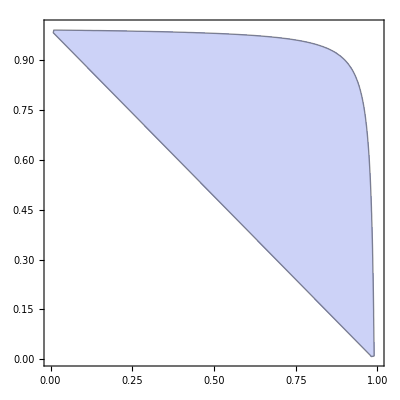

```mathematica
PR1["Use RegionPlot to display region of integration for: ",sub=α->.1,
NL,tmp1=RuleX[tmpxlim,xCos[1,2]]//First;
tmp2=tmp1/.Rule->GreaterEqual/.xCos[_,_]->1;
tmp3=tmp1/.Rule->LessEqual/.xCos[_,_]->-1;
tmp=tmp2&&tmp3&&1>Subscript[x, 1]>0&&1>Subscript[x, 2]>0/.sub
];
RegionPlot[tmp,{Subscript[x, 1],0,1},{Subscript[x, 2],0,1}]
```

(c) Feynman diagram for {e^+e^-}->{q q g}

```mathematica
PR1["Feynman diagram for ",{SuperPlus[e],SuperMinus[e]}->{q̄,q,g}
]
```

Feynman diagram for {e^+,e^-}→{q̄,q,g}

General graphic definitions for array points and lines.

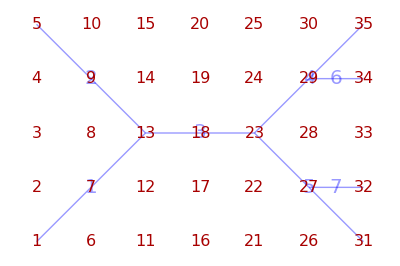

```mathematica
{vx,line}=GraphicPointLines[7,5,{{1,13},{5,13},{13,23},{23,35},{23,31},{29,34},{27,32}}];
```

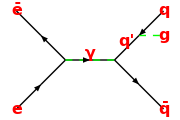
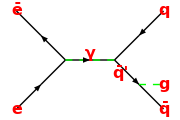

```mathematica
Linex[i_]:=Line[line[[i]]];
font:={Red,Bold,16};
{Graphics[{Thin,Black,
MidArrow[line[[1]]],
MidArrow[line[[2]]//Reverse],
MidArrow[line[[3]]],
MidArrow[line[[4]]//Reverse],
MidArrow[line[[5]]],
{Dashed,Green,Thick,Linex[3]},
{Dashed,Green,Thick,Linex[6]},
Text[Style[e,font],vx[[1]]],
Text[Style[ē,font],vx[[5]]],
Text[Style[q,font],vx[[35]]],
Text[Style[q̄,font],vx[[31]]],
Text[Style[g,font],vx[[34]]],
MidLineTextOffset[q',line[[4]],font,{-.5,-.25}],
Text[Style[γ,font],vx[[18]]+{0,.25}]
},ImageSize->Small],
Graphics[{Thin,Black,
MidArrow[line[[1]]],
MidArrow[line[[2]]//Reverse],
MidArrow[line[[3]]],
MidArrow[line[[4]]//Reverse],
MidArrow[line[[5]]],
{Dashed,Green,Thick,Linex[3]},
{Dashed,Green,Thick,Linex[7]},
Text[Style[e,font],vx[[1]]],
Text[Style[ē,font],vx[[5]]],
Text[Style[q,font],vx[[35]]],
Text[Style[q̄,font],vx[[31]]],
Text[Style[g,font],vx[[32]]],
MidLineTextOffset[q̄',line[[5]],font,{-.75,.45}],
Text[Style[γ,font],vx[[18]]+{0,.25}]
},ImageSize->Small]}
```

```mathematica
PR1["The scattering amplitude: ",
tmp0=T[L,"dd",{μ,ν}]. IntegralOp[{Subscript[Π, 3]},T[H,"uu",{μ,ν}]],
NL,"From: ",sub=tmp0[[2]]->(g@uu[μ,ν]-q@u[μ]q@u[ν]/(q@u[α]q@d[α])). H,
Yield,sub1=Map[g@dd[μ,ν]#&,sub]/.Dot->Times,
yield,sub1=sub1/.IntegralOp[a_,b_]c_->IntegralOp[a,b c]//Expand,
yield,sub1=MapAt[MetricContractAll[g,4][#]&,sub1/.α->ν,2],
yield,sub1=Map[#/3&,sub1],
NL,"Hence: ",tmp=tmp0,
yield,tmp=tmp/.sub/.Dot->Times//Expand,
NL,"Since current conservation",imply,sub=T[L,"dd",{μ,ν}]q@u[μ]->0,
Imply,tmp=tmp0->(tmp/.sub),
imply,(tmp/.Reverse[sub1])
]
```

The scattering amplitude: L_μν^μν.∫_Π_3 [H_μν^μν]
From: ∫_Π_3 [H_μν^μν]→(g_μν^μν-(q_μ^μ q_ν^ν)/(q_α^α q_α^α)).H
→ ∫_Π_3 [H_μν^μν] g_μν^μν→H g_μν^μν (g_μν^μν-(q_μ^μ q_ν^ν)/(q_α^α q_α^α)) ⟶ ∫_Π_3 [g_μν^μν H_μν^μν]→H g_μν^μν g_μν^μν-(H g_μν^μν q_μ^μ q_ν^ν)/(q_α^α q_α^α) ⟶ ∫_Π_3 [g_μν^μν H_μν^μν]→3 H ⟶ 1/3 ∫_Π_3 [g_μν^μν H_μν^μν]→H
Hence: L_μν^μν.∫_Π_3 [H_μν^μν] ⟶ H g_μν^μν L_μν^μν-(H L_μν^μν q_μ^μ q_ν^ν)/(q_α^α q_α^α)
Since current conservation ⇒ L_μν^μν q_μ^μ→0
⇒ L_μν^μν.∫_Π_3 [H_μν^μν]→H g_μν^μν L_μν^μν ⇒ L_μν^μν.∫_Π_3 [(1/3 ∫_Π_3 [g_μν^μν H_μν^μν])_μν^μν]→1/3 ∫_Π_3 [g_μν^μν H_μν^μν] g_μν^μν L_μν^μν

```mathematica
PR1["Differential cross section(electron-electron portion):",
tmpM=I T[Subscript[ℳ, e],"d"][μ]->I Q . v̄[Subscript[p, SuperPlus[e]]] .γ@d[μ]. u[Subscript[p, SuperMinus[e]]],
NL,"with realscalars: ",
realscalar={ℳ,Q,Subscript[m, _],T[Subscript[p, _],"d"][_],T[η,"du"][_,_],T[η,"dd"][_,_]},
Yield,tmp=Map[ConjugateTranspose[#]. ReplaceIndexTU[μ,ν][#]&,tmpM] //ConjugateCTSimplify1[realscalar,realscalar],
Yield,tmp=tmp/.simpleGamma//.scatteringAmplitudeRules//GammaRight[γ@d[μ]],
NL,"Expand Slash: ",tmp=tmp/.Slash[p_]:>γ@u[tmpi=Unique[]]T[p,"d"][tmpi]//.simpleDot2[realscalar],
NL,"Average over spins->Tr[]",
Yield,tmp=Map[Tr[#]&,tmp],
Yield,tmp=tmp//.simpleTr2[realscalar]//.tr:Tr[a__]:>RaiseTrγIndices[tr]//simpleTrGamma,
NL,"Contract with : ",g@uu[μ,ν]," for ",g@uu[μ,ν]T[L,"dd",{μ,ν}],
Yield,tmp=Map[g@uu[μ,ν]#&,tmp]//Expand,
Yield,tmp=MapAt[ContractUpDn[g][#]&,tmp,2]//Simplify,
Yield,tmp=MapAt[GroupTimeSpaceProducts[#]&,tmp,2]/.xDot->Times,

NL,"Assume: ",sub={Subscript[m, SuperPlus[e]]->Subscript[m, e],Subscript[m, SuperMinus[e]]->Subscript[m, e],T[Subscript[p, SuperPlus[e]],"d"][timespace@1]->-T[Subscript[p, SuperMinus[e]],"d"][timespace@1],T[Subscript[p, SuperPlus[e]],"d"][timespace@0]->T[Subscript[p, SuperMinus[e]],"d"][timespace@0],T[Subscript[p, SuperMinus[e]],"d"][timespace@1]->-T[Subscript[p, SuperMinus[e]],"u"][timespace@1],T[Subscript[p, SuperMinus[e]],"d"][timespace@0]->T[Subscript[p, SuperMinus[e]],"u"][timespace@0],
T[Subscript[p, SuperMinus[e]],"u"][timespace@1]^2->T[Subscript[p, SuperMinus[e]],"u"][timespace@0]^2-Subscript[m, e]^2
},
Imply,tmp=tmp/.sub,
Imply,tmp=tmp/.sub,
Imply,tmp=tmp/.sub//Expand
]
```

Differential cross section(electron-electron portion):ⅈ ℳ_e_μ^μ→ⅈ Q.v̄[p_(e^+)].γ_μ^μ.u[p_(e^-)]
with realscalars: {ℳ,Q,m__,p____^_,η___^__,η___^__}
→ (ℳ_e_μ^μ)^†.ℳ_e_ν^ν→Q^2 u[p_(e^-)]^†.(γ_μ^μ)^†.(v̄[p_(e^+)])^†.v̄[p_(e^+)].γ_ν^ν.u[p_(e^-)]
→ (ℳ_e_μ^μ)^†.ℳ_e_ν^ν→-Q^2 m_(e^-).γ_μ^μ.m_(e^+).γ_ν^ν+Q^2 m_(e^-).γ_μ^μ.(γ_($600)^($600) (p_(e^+))_($600)^($600)).γ_ν^ν-Q^2 (γ_($599)^($599) (p_(e^-))_($599)^($599)).γ_μ^μ.m_(e^+).γ_ν^ν+Q^2 (γ_($599)^($599) (p_(e^-))_($599)^($599)).γ_μ^μ.(γ_($600)^($600) (p_(e^+))_($600)^($600)).γ_ν^ν
Expand Slash: (ℳ_e_μ^μ)^†.ℳ_e_ν^ν→-Q^2 γ_μ^μ.γ_ν^ν m_(e^-) m_(e^+)-Q^2 γ_($599)^($599).γ_μ^μ.γ_ν^ν m_(e^+) (p_(e^-))_($599)^($599)+Q^2 γ_μ^μ.γ_($600)^($600).γ_ν^ν m_(e^-) (p_(e^+))_($600)^($600)+Q^2 γ_($599)^($599).γ_μ^μ.γ_($600)^($600).γ_ν^ν (p_(e^-))_($599)^($599) (p_(e^+))_($600)^($600)
Average over spins->Tr[]
→ Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→Tr[-Q^2 γ_μ^μ.γ_ν^ν m_(e^-) m_(e^+)-Q^2 γ_($599)^($599).γ_μ^μ.γ_ν^ν m_(e^+) (p_(e^-))_($599)^($599)+Q^2 γ_μ^μ.γ_($600)^($600).γ_ν^ν m_(e^-) (p_(e^+))_($600)^($600)+Q^2 γ_($599)^($599).γ_μ^μ.γ_($600)^($600).γ_ν^ν (p_(e^-))_($599)^($599) (p_(e^+))_($600)^($600)]
→ Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→-4 Q^2 m_(e^-) m_(e^+) g_μ$601^μ$601 g_ν$602^ν$602 g_($601$602)^($601$602)+4 Q^2 g_μ$607^μ$607 g_ν$608^ν$608 (g_($599$607)^($599$607) g_($600$608)^($600$608)+g_($599$608)^($599$608) g_($607$600)^($607$600)-g_($599$600)^($599$600) g_($607$608)^($607$608)) (p_(e^-))_($599)^($599) (p_(e^+))_($600)^($600)
Contract with : g_μν^μν for g_μν^μν L_μν^μν
→ g_μν^μν Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→-4 Q^2 m_(e^-) m_(e^+) g_μ$601^μ$601 g_ν$602^ν$602 g_μν^μν g_($601$602)^($601$602)+4 Q^2 g_μ$607^μ$607 g_ν$608^ν$608 g_μν^μν g_($599$607)^($599$607) g_($600$608)^($600$608) (p_(e^-))_($599)^($599) (p_(e^+))_($600)^($600)+4 Q^2 g_μ$607^μ$607 g_ν$608^ν$608 g_μν^μν g_($599$608)^($599$608) g_($607$600)^($607$600) (p_(e^-))_($599)^($599) (p_(e^+))_($600)^($600)-4 Q^2 g_μ$607^μ$607 g_ν$608^ν$608 g_μν^μν g_($599$600)^($599$600) g_($607$608)^($607$608) (p_(e^-))_($599)^($599) (p_(e^+))_($600)^($600)
→ g_μν^μν Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→4 Q^2 (-4 m_(e^-) m_(e^+)-4 (p_(e^-))_($600)^($600) (p_(e^+))_($600)^($600)+(p_(e^-))_($608)^($608) (p_(e^+))_($608)^($608)+(p_(e^-))_($608)^($608) (p_(e^+))_($608)^($608))
→ g_μν^μν Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→-16 Q^2 m_(e^-) m_(e^+)-12 Q^2 (p_(e^-))_0^0 (p_(e^+))_0^0-12 Q^2 (p_(e^-))_1^1 (p_(e^+))_1^1+4 Q^2 (p_(e^-))_0^0 (p_(e^+))_0^0+4 Q^2 (p_(e^-))_1^1 (p_(e^+))_1^1
Assume: {m_(e^+)→m_e,m_(e^-)→m_e,(p_(e^+))_1^1→-(p_(e^-))_1^1,(p_(e^+))_0^0→(p_(e^-))_0^0,(p_(e^-))_1^1→-(p_(e^-))_1^1,(p_(e^-))_0^0→(p_(e^-))_0^0,((p_(e^-))_1^1)^2→-m_e^2+((p_(e^-))_0^0)^2}
⇒ g_μν^μν Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→-16 Q^2 m_e^2-12 Q^2 (p_(e^-))_0^0 (p_(e^-))_0^0+12 Q^2 (p_(e^-))_1^1 (p_(e^-))_1^1+4 Q^2 (p_(e^-))_0^0 (p_(e^+))_0^0-4 Q^2 (p_(e^-))_1^1 (p_(e^+))_1^1
⇒ g_μν^μν Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→-16 Q^2 m_e^2-12 Q^2 ((p_(e^-))_0^0)^2-12 Q^2 ((p_(e^-))_1^1)^2+4 Q^2 (p_(e^-))_0^0 (p_(e^+))_0^0-4 Q^2 (p_(e^-))_1^1 (p_(e^+))_1^1
⇒ g_μν^μν Tr[(ℳ_e_μ^μ)^†.ℳ_e_ν^ν]→-4 Q^2 m_e^2-24 Q^2 ((p_(e^-))_0^0)^2+4 Q^2 (p_(e^-))_0^0 (p_(e^+))_0^0-4 Q^2 (p_(e^-))_1^1 (p_(e^+))_1^1

```mathematica
PR1["The amplitude for ",T[H,"uu"][μ,ν],
NL,"Has scattering amplitude: ",
tmpM=I T[Subscript[ℳ, H],"d"][μ]->I Subscript[Q, q] . v̄[Subscript[p, q̄]] .γ@d[μ].(I(Slash[Subscript[p, q']]+Subscript[m, q])/ (T[Subscript[p, q'],"u"][α]T[Subscript[p, q'],"d"][α]-Subscript[m, q]^2) ).(I G T[t,"u"][a]). u[Subscript[p, q]]+I Subscript[Q, q] . v̄[Subscript[p, q̄]] .(I G T[t,"u"][a]).(I(Slash[Subscript[p, q̄']]+Subscript[m, q])/ (T[Subscript[p, q̄'],"u"][α]T[Subscript[p, q̄'],"d"][α]-Subscript[m, q]^2) ).γ@d[μ]. u[Subscript[p, q]],
NL,"Assigning realscalars: ",
realscalar={Subscript[ℳ, H],Subscript[Q, _],Subscript[m, _],T[Subscript[p, _],"d"][_],T[Subscript[p, _],"u"][_],T[η,"du"][_,_],T[η,"dd"][_,_],G,1/X_},
NL,"Compute absolute Magnitude: ",imply,
tmp=Map[ConjugateTranspose[#].ReplaceIndexTU[a,b][ ReplaceIndexTU[μ,ν][#]]&,tmpM] //ConjugateCTSimplify1[realscalar,realscalar]//Expand,
"POFF",
NL,"Separate color gauge terms: ",
tmp=tmp/.dd:Dot[_,_]:>MoveDotRight[  T[t,"u"][b],  { } ][dd];
tmp=tmp/.dd:Dot[_,_]:>MoveDotRight[ ConjugateTranspose[ T[t,"u"][a]],  { t} ][dd];
tmp=MapAt[#/.dd:Dot[_,_]:>dd[[1;;-3]]dd[[-2;;-1]]&,tmp,2],
sub={V_[p_].OverBar[V_][p_]->Slash[p]-Subscript[m, p],
ConjugateTranspose[OverBar[U_][a_]]->γ@u[0]. U[a],HoldPattern[Dot[(OverBar[U_])[p_],a__,U_[p_]]]:>a.(Slash[p]+Subscript[m, p])/;!FreeQ[U,u|v],
HoldPattern[Dot[ConjugateTranspose[U_[p_]],a__,U_[p_]]]:>γ@u[0]. a .(Slash[p]+Subscript[m, p])/;!FreeQ[U,u|v] ,Slash[p_]:>γ@u[$i=Unique[]]T[p,"d"][$i],
T[p1_,"d"][i_]T[p2_,"u"][i_]:>Sort[p1 . p2]/;!FreeQ[p1,p]&&!FreeQ[p2,p]
};
Yield,tmp=tmp//.sub//.simpleDot2[realscalar]//.simpleGamma/.g@uu[0,0]->1//.simpleDot2[realscalar]//ConjugateCTSimplify1[realscalar,realscalar]//Expand;
tmp=ConjugateSimplify[tmp,{Subscript[p, _]}],
NL,"Adjust up-down indices so that γ indices are all down so that Tr[] Rule[]s work.",
tmp=tmp//.dd:(Dot[a_,b_]T[p_,"d"][i_]):>UpDownIndexSwap[i][dd]/;ListFreeQ[dd,{t}]/.γ@u[0]->γ@d[0],
NL,"Add Tr[] to γ matrices: ",
Yield,tmp=tmp/.dd:Dot[_,_]:>Tr[dd]/;!FreeQ[dd,γ],
Yield,tmp=tmp//.simpleGamma/.g@dd[0,0]->1//.simpleDot2[{}]//Expand,
Yield,tmp1=tmp//.simpleGamma/.g@dd[0,0]->1//.simpleDot2[{}]//Expand,
NL,"Work on remaining Tr[] terms: ",
Yield,test=tmp=tmp1/.generateTrγ[6],
"PONdd",
Yield,tmp3=Map[ContractUpDn[g][g@uu[μ,ν]#]&,tmp]//.T[p1_,"d"][i_]T[p2_,"u"][i_]:>Sort[p1 . p2]//Simplify
]
```

The amplitude for H_μν^μν
Has scattering amplitude: ⅈ ℳ_H_μ^μ→ⅈ Q_q.v̄[p_(q̄)].(ⅈ G t_a^a).(ⅈ (/p_(q̄')+m_q))/(-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α).γ_μ^μ.u[p_q]+ⅈ Q_q.v̄[p_(q̄)].γ_μ^μ.(ⅈ (/p_q'+m_q))/(-m_q^2+p_q'_α^α p_q'_α^α).(ⅈ G t_a^a).u[p_q]
Assigning realscalars: {ℳ_H,Q__,m__,p____^_,p____^_,η___^__,η___^__,G,1/X_}
Compute absolute Magnitude:  ⇒ (ℳ_H_μ^μ)^†.ℳ_H_ν^ν→(G^2 u[p_q]^†.(t_a^a)^†.(/p_q')^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.(/p_q').t_b^b.u[p_q] Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(t_a^a)^†.(/p_q')^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.t_b^b.u[p_q] m_q Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(t_a^a)^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.(/p_q').t_b^b.u[p_q] m_q Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(t_a^a)^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.t_b^b.u[p_q] m_q^2 Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(/p_(q̄'))^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.(/p_q').t_b^b.u[p_q] Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(/p_(q̄'))^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.t_b^b.u[p_q] m_q Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.(/p_q').t_b^b.u[p_q] m_q Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].γ_ν^ν.t_b^b.u[p_q] m_q^2 Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+p_q'_α^α p_q'_α^α))+(G^2 u[p_q]^†.(t_a^a)^†.(/p_q')^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.(/p_(q̄')).γ_ν^ν.u[p_q] Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))+(G^2 u[p_q]^†.(t_a^a)^†.(/p_q')^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.γ_ν^ν.u[p_q] m_q Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))+(G^2 u[p_q]^†.(t_a^a)^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.(/p_(q̄')).γ_ν^ν.u[p_q] m_q Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))+(G^2 u[p_q]^†.(t_a^a)^†.(γ_μ^μ)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.γ_ν^ν.u[p_q] m_q^2 Q_q^2)/(((p_q'_α^α p_q'_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(/p_(q̄'))^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.(/p_(q̄')).γ_ν^ν.u[p_q] Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(/p_(q̄'))^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.γ_ν^ν.u[p_q] m_q Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.(/p_(q̄')).γ_ν^ν.u[p_q] m_q Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))+(G^2 u[p_q]^†.(γ_μ^μ)^†.(t_a^a)^†.(v̄[p_(q̄)])^†.v̄[p_(q̄)].t_b^b.γ_ν^ν.u[p_q] m_q^2 Q_q^2)/((((p_(q̄'))_α^α (p_(q̄'))_α^α)^*-m_q^2) (-m_q^2+(p_(q̄'))_α^α (p_(q̄'))_α^α))
.......
→ (ℳ_H_ν^ν)^†.ℳ_H_ν^ν→-(8 G^2 (t_a^a)^†.t_b^b (-p_q.p_(q̄) (p_q'.p_q')^2 p_(q̄').p_(q̄')-p_q.p_(q̄) p_q'.p_q' (p_(q̄').p_(q̄'))^2+p_q.p_(q̄) (p_q'.p_q')^2 m_q^2+6 p_q.p_(q̄) p_q'.p_q' p_(q̄').p_(q̄') m_q^2+p_q.p_(q̄) (p_(q̄').p_(q̄'))^2 m_q^2-5 p_q.p_(q̄) p_q'.p_q' m_q^4-5 p_q.p_(q̄) p_(q̄').p_(q̄') m_q^4+4 p_q.p_(q̄) m_q^6-4 p_(q̄).p_(q̄') (p_q'.p_q')^2 m_q m_p_q+2 p_(q̄).p_q' p_q'.p_q' p_(q̄').p_(q̄') m_q m_p_q-4 p_(q̄).p_(q̄') p_q'.p_q' p_(q̄').p_(q̄') m_q m_p_q+2 p_(q̄).p_q' (p_(q̄').p_(q̄'))^2 m_q m_p_q-2 p_(q̄).p_q' p_q'.p_q' m_q^3 m_p_q+12 p_(q̄).p_(q̄') p_q'.p_q' m_q^3 m_p_q-6 p_(q̄).p_q' p_(q̄').p_(q̄') m_q^3 m_p_q+4 p_(q̄).p_(q̄') p_(q̄').p_(q̄') m_q^3 m_p_q+4 p_(q̄).p_q' m_q^5 m_p_q-8 p_(q̄).p_(q̄') m_q^5 m_p_q+2 (p_q'.p_q')^2 p_(q̄').p_(q̄') m_p_q m_(p_(q̄))-2 p_q'.p_q' p_q'.p_(q̄') p_(q̄').p_(q̄') m_p_q m_(p_(q̄))+2 p_q'.p_q' (p_(q̄').p_(q̄'))^2 m_p_q m_(p_(q̄))+2 (p_q'.p_q')^2 m_q^2 m_p_q m_(p_(q̄))+2 p_q'.p_q' p_q'.p_(q̄') m_q^2 m_p_q m_(p_(q̄))-4 p_q'.p_q' p_(q̄').p_(q̄') m_q^2 m_p_q m_(p_(q̄))+2 p_q'.p_(q̄') p_(q̄').p_(q̄') m_q^2 m_p_q m_(p_(q̄))+2 (p_(q̄').p_(q̄'))^2 m_q^2 m_p_q m_(p_(q̄))-6 p_q'.p_q' m_q^4 m_p_q m_(p_(q̄))-2 p_q'.p_(q̄') m_q^4 m_p_q m_(p_(q̄))-6 p_(q̄').p_(q̄') m_q^4 m_p_q m_(p_(q̄))+8 m_q^6 m_p_q m_(p_(q̄))-2 p_q.p_(q̄') (p_q'.p_q'-m_q^2) (p_(q̄).p_(q̄') (-p_q'.p_q'+m_q^2)+m_q (p_q'.p_q'+p_(q̄').p_(q̄')-2 m_q^2) m_(p_(q̄)))+2 p_q.p_q' (p_(q̄').p_(q̄')-m_q^2) (-2 p_(q̄).p_(q̄') (p_q'.p_q'-m_q^2)+p_(q̄).p_q' (p_(q̄').p_(q̄')-m_q^2)+2 m_q (p_q'.p_q'+p_(q̄').p_(q̄')-2 m_q^2) m_(p_(q̄)))) Q_q^2)/((p_q'.p_q'-m_q^2)^2 (p_(q̄').p_(q̄')-m_q^2)^2)

```mathematica
PR1["Massless quark assumption: ",subm={Subscript[m, Subscript[p, q_]]->Subscript[m, q],Subscript[xm, q|q̄]->0},
Imply,tmp=tmp3/.subm,
NL,"Propagator 4-momentum conservation: ",
sub={Subscript[p, q̄']->Subscript[p, q̄]+Subscript[p, g],Subscript[p, q']->Subscript[p, q]+Subscript[p, g]}//Flatten,
Imply,tmp=tmp/.sub//.simpleDot2[{}]/. dd:Dot[a_,b_]:>Sort[dd],
NL,"Apply invariant mass: ",
test=tmp4=tmp/. Subscript[p, a_]. Subscript[p, a_]->Subscript[m, a]^2  
];
```

Massless quark assumption: {m_p_q_→m_q,xm_(q|q̄)→0}
⇒ (ℳ_H_ν^ν)^†.ℳ_H_ν^ν→-(8 G^2 (t_a^a)^†.t_b^b (-p_q.p_(q̄) (p_q'.p_q')^2 p_(q̄').p_(q̄')-p_q.p_(q̄) p_q'.p_q' (p_(q̄').p_(q̄'))^2+p_q.p_(q̄) (p_q'.p_q')^2 m_q^2-4 p_(q̄).p_(q̄') (p_q'.p_q')^2 m_q^2+6 p_q.p_(q̄) p_q'.p_q' p_(q̄').p_(q̄') m_q^2+2 p_(q̄).p_q' p_q'.p_q' p_(q̄').p_(q̄') m_q^2-4 p_(q̄).p_(q̄') p_q'.p_q' p_(q̄').p_(q̄') m_q^2+p_q.p_(q̄) (p_(q̄').p_(q̄'))^2 m_q^2+2 p_(q̄).p_q' (p_(q̄').p_(q̄'))^2 m_q^2-5 p_q.p_(q̄) p_q'.p_q' m_q^4-2 p_(q̄).p_q' p_q'.p_q' m_q^4+12 p_(q̄).p_(q̄') p_q'.p_q' m_q^4-5 p_q.p_(q̄) p_(q̄').p_(q̄') m_q^4-6 p_(q̄).p_q' p_(q̄').p_(q̄') m_q^4+4 p_(q̄).p_(q̄') p_(q̄').p_(q̄') m_q^4+4 p_q.p_(q̄) m_q^6+4 p_(q̄).p_q' m_q^6-8 p_(q̄).p_(q̄') m_q^6+2 (p_q'.p_q')^2 p_(q̄').p_(q̄') m_q m_(q̄)-2 p_q'.p_q' p_q'.p_(q̄') p_(q̄').p_(q̄') m_q m_(q̄)+2 p_q'.p_q' (p_(q̄').p_(q̄'))^2 m_q m_(q̄)+2 (p_q'.p_q')^2 m_q^3 m_(q̄)+2 p_q'.p_q' p_q'.p_(q̄') m_q^3 m_(q̄)-4 p_q'.p_q' p_(q̄').p_(q̄') m_q^3 m_(q̄)+2 p_q'.p_(q̄') p_(q̄').p_(q̄') m_q^3 m_(q̄)+2 (p_(q̄').p_(q̄'))^2 m_q^3 m_(q̄)-6 p_q'.p_q' m_q^5 m_(q̄)-2 p_q'.p_(q̄') m_q^5 m_(q̄)-6 p_(q̄').p_(q̄') m_q^5 m_(q̄)+8 m_q^7 m_(q̄)-2 p_q.p_(q̄') (p_q'.p_q'-m_q^2) (p_(q̄).p_(q̄') (-p_q'.p_q'+m_q^2)+m_q (p_q'.p_q'+p_(q̄').p_(q̄')-2 m_q^2) m_(q̄))+2 p_q.p_q' (p_(q̄').p_(q̄')-m_q^2) (-2 p_(q̄).p_(q̄') (p_q'.p_q'-m_q^2)+p_(q̄).p_q' (p_(q̄').p_(q̄')-m_q^2)+2 m_q (p_q'.p_q'+p_(q̄').p_(q̄')-2 m_q^2) m_(q̄))) Q_q^2)/((p_q'.p_q'-m_q^2)^2 (p_(q̄').p_(q̄')-m_q^2)^2)
Propagator 4-momentum conservation: {p_(q̄')→p_g+p_(q̄),p_q'→p_g+p_q}
⇒ (ℳ_H_ν^ν)^†.ℳ_H_ν^ν→-(8 G^2 (t_a^a)^†.t_b^b (-(p_g.p_g+2 p_g.p_q+p_q.p_q)^2 p_q.p_(q̄) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄))-(p_g.p_g+2 p_g.p_q+p_q.p_q) p_q.p_(q̄) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄))^2+(p_g.p_g+2 p_g.p_q+p_q.p_q)^2 p_q.p_(q̄) m_q^2-4 (p_g.p_g+2 p_g.p_q+p_q.p_q)^2 (p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^2+6 (p_g.p_g+2 p_g.p_q+p_q.p_q) p_q.p_(q̄) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^2+2 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_(q̄)+p_q.p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^2-4 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_(q̄)+p_(q̄).p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^2+p_q.p_(q̄) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄))^2 m_q^2+2 (p_g.p_(q̄)+p_q.p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄))^2 m_q^2-5 (p_g.p_g+2 p_g.p_q+p_q.p_q) p_q.p_(q̄) m_q^4-2 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_(q̄)+p_q.p_(q̄)) m_q^4+12 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^4-5 p_q.p_(q̄) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^4-6 (p_g.p_(q̄)+p_q.p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^4+4 (p_g.p_(q̄)+p_(q̄).p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^4+4 p_q.p_(q̄) m_q^6+4 (p_g.p_(q̄)+p_q.p_(q̄)) m_q^6-8 (p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^6+2 (p_g.p_g+2 p_g.p_q+p_q.p_q)^2 (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q m_(q̄)-2 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_g+p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q m_(q̄)+2 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄))^2 m_q m_(q̄)+2 (p_g.p_g+2 p_g.p_q+p_q.p_q)^2 m_q^3 m_(q̄)+2 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_g+p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)) m_q^3 m_(q̄)-4 (p_g.p_g+2 p_g.p_q+p_q.p_q) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^3 m_(q̄)+2 (p_g.p_g+p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^3 m_(q̄)+2 (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄))^2 m_q^3 m_(q̄)-6 (p_g.p_g+2 p_g.p_q+p_q.p_q) m_q^5 m_(q̄)-2 (p_g.p_g+p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)) m_q^5 m_(q̄)-6 (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)) m_q^5 m_(q̄)+8 m_q^7 m_(q̄)-2 (p_g.p_q+p_q.p_(q̄)) (p_g.p_g+2 p_g.p_q+p_q.p_q-m_q^2) ((p_g.p_(q̄)+p_(q̄).p_(q̄)) (-p_g.p_g-2 p_g.p_q-p_q.p_q+m_q^2)+m_q (2 p_g.p_g+2 p_g.p_q+2 p_g.p_(q̄)+p_q.p_q+p_(q̄).p_(q̄)-2 m_q^2) m_(q̄))+2 (p_g.p_q+p_q.p_q) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)-m_q^2) (-2 (p_g.p_(q̄)+p_(q̄).p_(q̄)) (p_g.p_g+2 p_g.p_q+p_q.p_q-m_q^2)+(p_g.p_(q̄)+p_q.p_(q̄)) (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)-m_q^2)+2 m_q (2 p_g.p_g+2 p_g.p_q+2 p_g.p_(q̄)+p_q.p_q+p_(q̄).p_(q̄)-2 m_q^2) m_(q̄))) Q_q^2)/((p_g.p_g+2 p_g.p_q+p_q.p_q-m_q^2)^2 (p_g.p_g+2 p_g.p_(q̄)+p_(q̄).p_(q̄)-m_q^2)^2)
Apply invariant mass: (ℳ_H_ν^ν)^†.ℳ_H_ν^ν→-(8 G^2 (t_a^a)^†.t_b^b (4 p_q.p_(q̄) m_q^6+4 (p_g.p_(q̄)+p_q.p_(q̄)) m_q^6-5 p_q.p_(q̄) m_q^4 (2 p_g.p_q+m_g^2+m_q^2)-2 (p_g.p_(q̄)+p_q.p_(q̄)) m_q^4 (2 p_g.p_q+m_g^2+m_q^2)+p_q.p_(q̄) m_q^2 (2 p_g.p_q+m_g^2+m_q^2)^2-2 (p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)+m_g^2) m_q^5 m_(q̄)+8 m_q^7 m_(q̄)+2 (p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)+m_g^2) m_q^3 (2 p_g.p_q+m_g^2+m_q^2) m_(q̄)-6 m_q^5 (2 p_g.p_q+m_g^2+m_q^2) m_(q̄)+2 m_q^3 (2 p_g.p_q+m_g^2+m_q^2)^2 m_(q̄)-8 m_q^6 (p_g.p_(q̄)+m_(q̄)^2)+12 m_q^4 (2 p_g.p_q+m_g^2+m_q^2) (p_g.p_(q̄)+m_(q̄)^2)-4 m_q^2 (2 p_g.p_q+m_g^2+m_q^2)^2 (p_g.p_(q̄)+m_(q̄)^2)-5 p_q.p_(q̄) m_q^4 (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)-6 (p_g.p_(q̄)+p_q.p_(q̄)) m_q^4 (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)+6 p_q.p_(q̄) m_q^2 (2 p_g.p_q+m_g^2+m_q^2) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)+2 (p_g.p_(q̄)+p_q.p_(q̄)) m_q^2 (2 p_g.p_q+m_g^2+m_q^2) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)-p_q.p_(q̄) (2 p_g.p_q+m_g^2+m_q^2)^2 (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)+2 (p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)+m_g^2) m_q^3 m_(q̄) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)-6 m_q^5 m_(q̄) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)-2 (p_g.p_q+p_g.p_(q̄)+p_q.p_(q̄)+m_g^2) m_q (2 p_g.p_q+m_g^2+m_q^2) m_(q̄) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)-4 m_q^3 (2 p_g.p_q+m_g^2+m_q^2) m_(q̄) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)+2 m_q (2 p_g.p_q+m_g^2+m_q^2)^2 m_(q̄) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)+4 m_q^4 (p_g.p_(q̄)+m_(q̄)^2) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)-4 m_q^2 (2 p_g.p_q+m_g^2+m_q^2) (p_g.p_(q̄)+m_(q̄)^2) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)+p_q.p_(q̄) m_q^2 (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)^2+2 (p_g.p_(q̄)+p_q.p_(q̄)) m_q^2 (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)^2-p_q.p_(q̄) (2 p_g.p_q+m_g^2+m_q^2) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)^2+2 m_q^3 m_(q̄) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)^2+2 m_q (2 p_g.p_q+m_g^2+m_q^2) m_(q̄) (2 p_g.p_(q̄)+m_g^2+m_(q̄)^2)^2-2 (p_g.p_q+p_q.p_(q̄)) (2 p_g.p_q+m_g^2) ((-2 p_g.p_q-m_g^2) (p_g.p_(q̄)+m_(q̄)^2)+m_q m_(q̄) (2 p_g.p_q+2 p_g.p_(q̄)+2 m_g^2-m_q^2+m_(q̄)^2))+2 (p_g.p_q+m_q^2) (2 p_g.p_(q̄)+m_g^2-m_q^2+m_(q̄)^2) (-2 (2 p_g.p_q+m_g^2) (p_g.p_(q̄)+m_(q̄)^2)+(p_g.p_(q̄)+p_q.p_(q̄)) (2 p_g.p_(q̄)+m_g^2-m_q^2+m_(q̄)^2)+2 m_q m_(q̄) (2 p_g.p_q+2 p_g.p_(q̄)+2 m_g^2-m_q^2+m_(q̄)^2))) Q_q^2)/((2 p_g.p_q+m_g^2)^2 (2 p_g.p_(q̄)+m_g^2-m_q^2+m_(q̄)^2)^2)

```mathematica
PR1["Switch labels: ",sub=p->k,and,
sub1={Subscript[k, q]->Subscript[k, 1],Subscript[k, q̄]->Subscript[k, 2],Subscript[k, g]->Subscript[k, 3],Subscript[m, g]->Subscript[m, 3],Subscript[m, q|q̄]->Subscript[m, 1]},and,
"back to Einstein notation: ",sub2=Dot[a_,b_]->T[a,"u"][μ]T[b,"d"][μ],
Imply,tmp=tmp4/.sub/.sub1/.sub2,
NL,"Apply x to k relationships: ",subq1,and;subq2;
Imply,tmp=tmp//.subq1/.subq2/.{Subscript[xm, 1|2]->0}/.Subscript[x, 3]->2-Subscript[x, 1]-Subscript[x, 2],
Imply,tmp=tmp//Simplify,
NL,"Integrate: ",test=tmp=IntegralOp[{{Subscript[x, 1],0,1},{Subscript[x, 2],1-Subscript[x, 1],1}},tmp[[2]]],(*
Imply,tmp=tmp/.subxIntegrate/.subIntegrate*)
]
```

Switch labels: p→k and {k_q→k_1,k_(q̄)→k_2,k_g→k_3,m_g→m_3,m_(q|q̄)→m_1} and back to Einstein notation: a_.b_→a_μ^μ b_μ^μ
⇒ ((ℳ_H_ν^ν)^†)_μ^μ (ℳ_H_ν^ν)_μ^μ→-(8 G^2 Q_q^2 ((t_a^a)^†)_μ^μ (8 m_1^8+4 m_1^6 k_1_μ^μ k_2_μ^μ-6 m_1^6 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)-5 m_1^4 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)+2 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2+m_1^2 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2-8 m_1^6 (m_1^2+k_2_μ^μ k_3_μ^μ)+12 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ)-4 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_1^2+k_2_μ^μ k_3_μ^μ)+4 m_1^6 (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ)-2 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ)-2 m_1^6 (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ)+2 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ)-6 m_1^6 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-5 m_1^4 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-4 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+6 m_1^2 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+4 m_1^4 (m_1^2+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-4 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-6 m_1^4 (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^4 (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^4 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2+m_1^2 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2+2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2-k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2+2 m_1^2 (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2-2 (k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ) (m_3^2+2 k_1_μ^μ k_3_μ^μ) ((-m_3^2-2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ)+m_1^2 (2 m_3^2+2 k_1_μ^μ k_3_μ^μ+2 k_2_μ^μ k_3_μ^μ))+2 (m_1^2+k_1_μ^μ k_3_μ^μ) (m_3^2+2 k_2_μ^μ k_3_μ^μ) (-2 (m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ)+(k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^2 (2 m_3^2+2 k_1_μ^μ k_3_μ^μ+2 k_2_μ^μ k_3_μ^μ))) (t_b^b)_μ^μ)/((m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_3^2+2 k_2_μ^μ k_3_μ^μ)^2)
Apply x to k relationships: (k_($j_))_μ_^μ_ (k_($k_))_μ_^μ_→s/2-(m_($j)^2)/2-(m_($k)^2)/2+1/2 m_μ$12178[$j,$k]^2-1/2 s x_μ$12178[$j,$k]
⇒ ((ℳ_H_ν^ν)^†)_μ^μ (ℳ_H_ν^ν)_μ^μ→-(8 G^2 Q_q^2 (8 m_1^8-8 m_1^6 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2)-6 m_1^6 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))+4 m_1^4 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))+2 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2+4 m_1^6 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2))-5 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2))+m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2))+4 m_1^6 (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))-6 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))-2 m_1^6 ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2)+2 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2)-6 m_1^6 (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+12 m_1^4 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-4 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-4 m_1^2 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-5 m_1^4 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+6 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-(m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-2 m_1^4 (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^4 ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^4 (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2-4 m_1^2 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2+m_1^2 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2-(m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2-2 (s-m_1^2-1/2 s (2-x_1-x_2)-(s x_2)/2) (m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2)) ((s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (-m_3^2-2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+m_1^2 (2 m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2)))+2 (m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2+m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2) ((m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))-2 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^2 (2 m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2)))) ((t_a^a)^†)_μ^μ (t_b^b)_μ^μ)/((m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2)
⇒ ((ℳ_H_ν^ν)^†)_μ^μ (ℳ_H_ν^ν)_μ^μ→-(4 G^2 Q_q^2 (8 m_1^8-4 m_2^8+2 m_2^6 (m_3^2+4 s (-x_1+x_2))-2 m_1^6 (6 m_2^2+3 m_3^2+2 s (-9+5 x_1+3 x_2))+m_2^4 (2 m_3^4+2 s m_3^2 (-3+2 x_1)-s^2 (-4+5 x_1^2+x_1 (4-14 x_2)+4 x_2+5 x_2^2))+m_1^4 (-4 m_2^4+2 m_3^4+2 s m_3^2 (-11+8 x_1+2 x_2)+2 m_2^2 (7 m_3^2+4 s (-7+2 x_1+4 x_2))+s^2 (24+11 x_1^2+4 x_2-9 x_2^2+2 x_1 (-22+7 x_2)))+s^2 (-2 m_3^4 (-1+x_1) (-1+x_2)+s^2 (-1+x_1) (x_1-x_2)^2 (-1+x_2)+s m_3^2 (2+x_1^2 (1-2 x_2)-4 x_2+x_2^2-2 x_1 (2-4 x_2+x_2^2)))+s m_2^2 (2 m_3^4 (x_1-x_2)+s m_3^2 (2-8 x_1+3 x_1^2+4 x_2-x_2^2)+s^2 (-x_1^3+x_1^2 (-4+7 x_2)+x_1 (4-7 x_2^2)+x_2 (-4+4 x_2+x_2^2)))+m_1^2 (12 m_2^6+2 m_2^4 (-5 m_3^2+2 s (5+3 x_1-7 x_2))+2 m_2^2 (-2 m_3^4-2 s m_3^2 (-7+5 x_1+x_2)+s^2 (-10+x_1^2+7 x_2^2-2 x_1 (-8+7 x_2)))+s (-2 m_3^4 (x_1-x_2)+s m_3^2 (10-5 x_1^2-24 x_2+7 x_2^2+x_1 (4+8 x_2))+s^2 (-4+x_1^3+x_1^2 (4-3 x_2)+16 x_2-8 x_2^2-x_2^3+x_1 x_2 (-16+11 x_2))))) ((t_a^a)^†)_μ^μ (t_b^b)_μ^μ)/((s+m_1^2-m_2^2-s x_1)^2 (m_1^2-m_2^2+s (-1+x_2))^2)
Integrate: ∫_({x_1,0,1}
{x_2,1-x_1,1}) [-(4 G^2 Q_q^2 (8 m_1^8-4 m_2^8+2 m_2^6 (m_3^2+4 s (-x_1+x_2))-2 m_1^6 (6 m_2^2+3 m_3^2+2 s (-9+5 x_1+3 x_2))+m_2^4 (2 m_3^4+2 s m_3^2 (-3+2 x_1)-s^2 (-4+5 x_1^2+x_1 (4-14 x_2)+4 x_2+5 x_2^2))+m_1^4 (-4 m_2^4+2 m_3^4+2 s m_3^2 (-11+8 x_1+2 x_2)+2 m_2^2 (7 m_3^2+4 s (-7+2 x_1+4 x_2))+s^2 (24+11 x_1^2+4 x_2-9 x_2^2+2 x_1 (-22+7 x_2)))+s^2 (-2 m_3^4 (-1+x_1) (-1+x_2)+s^2 (-1+x_1) (x_1-x_2)^2 (-1+x_2)+s m_3^2 (2+x_1^2 (1-2 x_2)-4 x_2+x_2^2-2 x_1 (2-4 x_2+x_2^2)))+s m_2^2 (2 m_3^4 (x_1-x_2)+s m_3^2 (2-8 x_1+3 x_1^2+4 x_2-x_2^2)+s^2 (-x_1^3+x_1^2 (-4+7 x_2)+x_1 (4-7 x_2^2)+x_2 (-4+4 x_2+x_2^2)))+m_1^2 (12 m_2^6+2 m_2^4 (-5 m_3^2+2 s (5+3 x_1-7 x_2))+2 m_2^2 (-2 m_3^4-2 s m_3^2 (-7+5 x_1+x_2)+s^2 (-10+x_1^2+7 x_2^2-2 x_1 (-8+7 x_2)))+s (-2 m_3^4 (x_1-x_2)+s m_3^2 (10-5 x_1^2-24 x_2+7 x_2^2+x_1 (4+8 x_2))+s^2 (-4+x_1^3+x_1^2 (4-3 x_2)+16 x_2-8 x_2^2-x_2^3+x_1 x_2 (-16+11 x_2))))) ((t_a^a)^†)_μ^μ (t_b^b)_μ^μ)/((s+m_1^2-m_2^2-s x_1)^2 (m_1^2-m_2^2+s (-1+x_2))^2)]Null

Switch labels: p→k and {k_q→k_1,k_(q̄)→k_2,k_g→k_3,m_g→m_3,m_(q|q̄)→m_1} and back to Einstein notation: a_.b_→a_μ^μ b_μ^μ
⇒ ((ℳ_H_ν^ν)^†)_μ^μ (ℳ_H_ν^ν)_μ^μ→-(8 G^2 Q_q^2 ((t_a^a)^†)_μ^μ (8 m_1^8+4 m_1^6 k_1_μ^μ k_2_μ^μ-6 m_1^6 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)-5 m_1^4 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)+2 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2+m_1^2 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2-8 m_1^6 (m_1^2+k_2_μ^μ k_3_μ^μ)+12 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ)-4 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_1^2+k_2_μ^μ k_3_μ^μ)+4 m_1^6 (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ)-2 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ)-2 m_1^6 (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ)+2 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ)-6 m_1^6 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-5 m_1^4 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-4 m_1^4 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+6 m_1^2 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+4 m_1^4 (m_1^2+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-4 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-6 m_1^4 (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^4 (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)-2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_3^2+k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^4 (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2+m_1^2 k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2+2 m_1^2 (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2-k_1_μ^μ k_2_μ^μ (m_1^2+m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2+2 m_1^2 (k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_1^2+m_3^2+2 k_2_μ^μ k_3_μ^μ)^2-2 (k_1_μ^μ k_2_μ^μ+k_1_μ^μ k_3_μ^μ) (m_3^2+2 k_1_μ^μ k_3_μ^μ) ((-m_3^2-2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ)+m_1^2 (2 m_3^2+2 k_1_μ^μ k_3_μ^μ+2 k_2_μ^μ k_3_μ^μ))+2 (m_1^2+k_1_μ^μ k_3_μ^μ) (m_3^2+2 k_2_μ^μ k_3_μ^μ) (-2 (m_3^2+2 k_1_μ^μ k_3_μ^μ) (m_1^2+k_2_μ^μ k_3_μ^μ)+(k_1_μ^μ k_2_μ^μ+k_2_μ^μ k_3_μ^μ) (m_3^2+2 k_2_μ^μ k_3_μ^μ)+2 m_1^2 (2 m_3^2+2 k_1_μ^μ k_3_μ^μ+2 k_2_μ^μ k_3_μ^μ))) (t_b^b)_μ^μ)/((m_3^2+2 k_1_μ^μ k_3_μ^μ)^2 (m_3^2+2 k_2_μ^μ k_3_μ^μ)^2)
Apply x to k relationships: (k_($j_))_μ_^μ_ (k_($k_))_μ_^μ_→s/2-(m_($j)^2)/2-(m_($k)^2)/2+1/2 m_μ$12289[$j,$k]^2-1/2 s x_μ$12289[$j,$k]
⇒ ((ℳ_H_ν^ν)^†)_μ^μ (ℳ_H_ν^ν)_μ^μ→-(8 G^2 Q_q^2 (8 m_1^8-8 m_1^6 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2)-6 m_1^6 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))+4 m_1^4 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))+2 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2+4 m_1^6 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2))-5 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2))+m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2))+4 m_1^6 (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))-6 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))-2 m_1^6 ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2)+2 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2)-6 m_1^6 (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+12 m_1^4 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-4 m_1^4 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-4 m_1^2 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-5 m_1^4 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+6 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-(m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-2 m_1^4 (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^4 ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))-2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) ((3 s)/2-m_1^2/2-m_2^2/2+m_3^2/2-(s x_1)/2-1/2 s (2-x_1-x_2)-(s x_2)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^4 (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2-4 m_1^2 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2+2 m_1^2 (m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2+m_1^2 (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2-(m_1^2+m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2-m_1^2/2-m_2^2/2+m_3^2/2-1/2 s (2-x_1-x_2)) (m_1^2+m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2-2 (s-m_1^2-1/2 s (2-x_1-x_2)-(s x_2)/2) (m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2)) ((s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (-m_3^2-2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+m_1^2 (2 m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2)))+2 (m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s/2+m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2) ((m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)) (s-m_2^2-(s x_1)/2-1/2 s (2-x_1-x_2))-2 (s/2+(3 m_1^2)/2-m_2^2/2-m_3^2/2-(s x_1)/2) (m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))+2 m_1^2 (2 m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2)+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2)))) ((t_a^a)^†)_μ^μ (t_b^b)_μ^μ)/((m_3^2+2 (s/2+m_1^2/2-m_2^2/2-m_3^2/2-(s x_1)/2))^2 (m_3^2+2 (s/2-m_1^2/2+m_2^2/2-m_3^2/2-(s x_2)/2))^2)
⇒ ((ℳ_H_ν^ν)^†)_μ^μ (ℳ_H_ν^ν)_μ^μ→-(4 G^2 Q_q^2 (8 m_1^8-4 m_2^8+2 m_2^6 (m_3^2+4 s (-x_1+x_2))-2 m_1^6 (6 m_2^2+3 m_3^2+2 s (-9+5 x_1+3 x_2))+m_2^4 (2 m_3^4+2 s m_3^2 (-3+2 x_1)-s^2 (-4+5 x_1^2+x_1 (4-14 x_2)+4 x_2+5 x_2^2))+m_1^4 (-4 m_2^4+2 m_3^4+2 s m_3^2 (-11+8 x_1+2 x_2)+2 m_2^2 (7 m_3^2+4 s (-7+2 x_1+4 x_2))+s^2 (24+11 x_1^2+4 x_2-9 x_2^2+2 x_1 (-22+7 x_2)))+s^2 (-2 m_3^4 (-1+x_1) (-1+x_2)+s^2 (-1+x_1) (x_1-x_2)^2 (-1+x_2)+s m_3^2 (2+x_1^2 (1-2 x_2)-4 x_2+x_2^2-2 x_1 (2-4 x_2+x_2^2)))+s m_2^2 (2 m_3^4 (x_1-x_2)+s m_3^2 (2-8 x_1+3 x_1^2+4 x_2-x_2^2)+s^2 (-x_1^3+x_1^2 (-4+7 x_2)+x_1 (4-7 x_2^2)+x_2 (-4+4 x_2+x_2^2)))+m_1^2 (12 m_2^6+2 m_2^4 (-5 m_3^2+2 s (5+3 x_1-7 x_2))+2 m_2^2 (-2 m_3^4-2 s m_3^2 (-7+5 x_1+x_2)+s^2 (-10+x_1^2+7 x_2^2-2 x_1 (-8+7 x_2)))+s (-2 m_3^4 (x_1-x_2)+s m_3^2 (10-5 x_1^2-24 x_2+7 x_2^2+x_1 (4+8 x_2))+s^2 (-4+x_1^3+x_1^2 (4-3 x_2)+16 x_2-8 x_2^2-x_2^3+x_1 x_2 (-16+11 x_2))))) ((t_a^a)^†)_μ^μ (t_b^b)_μ^μ)/((s+m_1^2-m_2^2-s x_1)^2 (m_1^2-m_2^2+s (-1+x_2))^2)
Integrate: ∫_({x_1,0,1}
{x_2,1-x_1,1}) [-(4 G^2 Q_q^2 (8 m_1^8-4 m_2^8+2 m_2^6 (m_3^2+4 s (-x_1+x_2))-2 m_1^6 (6 m_2^2+3 m_3^2+2 s (-9+5 x_1+3 x_2))+m_2^4 (2 m_3^4+2 s m_3^2 (-3+2 x_1)-s^2 (-4+5 x_1^2+x_1 (4-14 x_2)+4 x_2+5 x_2^2))+m_1^4 (-4 m_2^4+2 m_3^4+2 s m_3^2 (-11+8 x_1+2 x_2)+2 m_2^2 (7 m_3^2+4 s (-7+2 x_1+4 x_2))+s^2 (24+11 x_1^2+4 x_2-9 x_2^2+2 x_1 (-22+7 x_2)))+s^2 (-2 m_3^4 (-1+x_1) (-1+x_2)+s^2 (-1+x_1) (x_1-x_2)^2 (-1+x_2)+s m_3^2 (2+x_1^2 (1-2 x_2)-4 x_2+x_2^2-2 x_1 (2-4 x_2+x_2^2)))+s m_2^2 (2 m_3^4 (x_1-x_2)+s m_3^2 (2-8 x_1+3 x_1^2+4 x_2-x_2^2)+s^2 (-x_1^3+x_1^2 (-4+7 x_2)+x_1 (4-7 x_2^2)+x_2 (-4+4 x_2+x_2^2)))+m_1^2 (12 m_2^6+2 m_2^4 (-5 m_3^2+2 s (5+3 x_1-7 x_2))+2 m_2^2 (-2 m_3^4-2 s m_3^2 (-7+5 x_1+x_2)+s^2 (-10+x_1^2+7 x_2^2-2 x_1 (-8+7 x_2)))+s (-2 m_3^4 (x_1-x_2)+s m_3^2 (10-5 x_1^2-24 x_2+7 x_2^2+x_1 (4+8 x_2))+s^2 (-4+x_1^3+x_1^2 (4-3 x_2)+16 x_2-8 x_2^2-x_2^3+x_1 x_2 (-16+11 x_2))))) ((t_a^a)^†)_μ^μ (t_b^b)_μ^μ)/((s+m_1^2-m_2^2-s x_1)^2 (m_1^2-m_2^2+s (-1+x_2))^2)]Null

```mathematica
tmp/.Integrate[int_,var_]->IntegralOp[{var},int]
%//SimpleIntegrand//ExtractPattern[#,IntegralOp[_,_]]&//First
```

∫_({x_1,0,1}
{x_2,1-x_1,1}) [-(4 G^2 Q_q^2 (8 m_1^8-4 m_2^8+2 m_2^6 (m_3^2+4 s (-x_1+x_2))-2 m_1^6 (6 m_2^2+3 m_3^2+2 s (-9+5 x_1+3 x_2))+m_2^4 (2 m_3^4+2 s m_3^2 (-3+2 x_1)-s^2 (-4+5 x_1^2+x_1 (4-14 x_2)+4 x_2+5 x_2^2))+m_1^4 (-4 m_2^4+2 m_3^4+2 s m_3^2 (-11+8 x_1+2 x_2)+2 m_2^2 (7 m_3^2+4 s (-7+2 x_1+4 x_2))+s^2 (24+11 x_1^2+4 x_2-9 x_2^2+2 x_1 (-22+7 x_2)))+s^2 (-2 m_3^4 (-1+x_1) (-1+x_2)+s^2 (-1+x_1) (x_1-x_2)^2 (-1+x_2)+s m_3^2 (2+x_1^2 (1-2 x_2)-4 x_2+x_2^2-2 x_1 (2-4 x_2+x_2^2)))+s m_2^2 (2 m_3^4 (x_1-x_2)+s m_3^2 (2-8 x_1+3 x_1^2+4 x_2-x_2^2)+s^2 (-x_1^3+x_1^2 (-4+7 x_2)+x_1 (4-7 x_2^2)+x_2 (-4+4 x_2+x_2^2)))+m_1^2 (12 m_2^6+2 m_2^4 (-5 m_3^2+2 s (5+3 x_1-7 x_2))+2 m_2^2 (-2 m_3^4-2 s m_3^2 (-7+5 x_1+x_2)+s^2 (-10+x_1^2+7 x_2^2-2 x_1 (-8+7 x_2)))+s (-2 m_3^4 (x_1-x_2)+s m_3^2 (10-5 x_1^2-24 x_2+7 x_2^2+x_1 (4+8 x_2))+s^2 (-4+x_1^3+x_1^2 (4-3 x_2)+16 x_2-8 x_2^2-x_2^3+x_1 x_2 (-16+11 x_2))))) ((t_a^a)^†)_μ^μ (t_b^b)_μ^μ)/((s+m_1^2-m_2^2-s x_1)^2 (m_1^2-m_2^2+s (-1+x_2))^2)]

∫_({x_1,0,1}
{x_2,1-x_1,1}) [(8 m_1^8-4 m_2^8+2 m_2^6 (m_3^2+4 s (-x_1+x_2))-2 m_1^6 (6 m_2^2+3 m_3^2+2 s (-9+5 x_1+3 x_2))+m_2^4 (2 m_3^4+2 s m_3^2 (-3+2 x_1)-s^2 (-4+5 x_1^2+x_1 (4-14 x_2)+4 x_2+5 x_2^2))+m_1^4 (-4 m_2^4+2 m_3^4+2 s m_3^2 (-11+8 x_1+2 x_2)+2 m_2^2 (7 m_3^2+4 s (-7+2 x_1+4 x_2))+s^2 (24+11 x_1^2+4 x_2-9 x_2^2+2 x_1 (-22+7 x_2)))+s^2 (-2 m_3^4 (-1+x_1) (-1+x_2)+s^2 (-1+x_1) (x_1-x_2)^2 (-1+x_2)+s m_3^2 (2+x_1^2 (1-2 x_2)-4 x_2+x_2^2-2 x_1 (2-4 x_2+x_2^2)))+s m_2^2 (2 m_3^4 (x_1-x_2)+s m_3^2 (2-8 x_1+3 x_1^2+4 x_2-x_2^2)+s^2 (-x_1^3+x_1^2 (-4+7 x_2)+x_1 (4-7 x_2^2)+x_2 (-4+4 x_2+x_2^2)))+m_1^2 (12 m_2^6+2 m_2^4 (-5 m_3^2+2 s (5+3 x_1-7 x_2))+2 m_2^2 (-2 m_3^4-2 s m_3^2 (-7+5 x_1+x_2)+s^2 (-10+x_1^2+7 x_2^2-2 x_1 (-8+7 x_2)))+s (-2 m_3^4 (x_1-x_2)+s m_3^2 (10-5 x_1^2-24 x_2+7 x_2^2+x_1 (4+8 x_2))+s^2 (-4+x_1^3+x_1^2 (4-3 x_2)+16 x_2-8 x_2^2-x_2^3+x_1 x_2 (-16+11 x_2)))))/((s+m_1^2-m_2^2-s x_1)^2 (m_1^2-m_2^2+s (-1+x_2))^2)]

```mathematica
FullSimplify[%8004]/.Subscript[m, _]->0
%/.subxIntegrate/.subIntegrate
%/.α->0
```

%8004

%8004

%8004